# Quasinormal modes (QNMs) of Reissner-Nordstrom black branes which are asymptotically AdS_5

by 
Stefan Janiszewski (University of Victoria)
and 
Matthias Kaminski (University of Alabama)

Last updated: December 04th, 2015

Summary of contents:
This is one of two notebooks accompanying the publication “Quasinormal modes of magnetic and electric black branes versus far from equilibrium anisotropic fluids” [http://arxiv.org/abs/arXiv:1508.06993]. Here we collect the full calculation of two kinds of quasinormal modes (QNMs) in the background of the Reissner-Nordstrom AdS5 black brane (RNAdS5). The first kind of QNMs considered are the ones associated with the tensor (spin 2) fluctuation h_xy (equivalently h_xx-h_yy at nonzero momentum in the z-direction, and at zero momentum, k=0, also equivalently h_xz, h_yz, h_xx-h_zz, h_yy-h_zz). The second kind of QNMs are the one associated with the vector (spin 1) fluctuations a_x  (equivalently a_y, a_z, h_tx, h_ty, h_tz)  at vanishing momentum k=0. We use two methods: the shooting method, and the continued fraction method. References to publications, figures, tables, and equation numbers, e.g. [19] and equation (1), refer to the references, figures, tables, and equations provided in the publication.

Usage:
In order to use this notebook to generate QNMs at desired values of charge density qt, momentum k in z-direction, follow these instructions: 
1. The accompanying files ``rulesHk14’’ and ``ruleaxHk14’’ need to be placed in a directory specified in the path variable as indicated below.
2. Evaluate all cells in sequence up to the Examples subsection.
3. Pick a desired value of momentum and charge, provide qnmRoutine[...] with a reasonable guess for that QNM value as indicated below where qnmRoutine[...] is defined. The Examples subsection shows how the parameters are changed and how different QNMs are obtained. 

Note that in order for the resulting QNM frequency to be trusted, one should pay close attention to error messages about accuracy, and check how the frequency value changes when accuracy, working precions, horizon location, boundary location are changed.

## Shooting method

```mathematica
Quit
```

### Set global parameters

Define precision and accuracy parameters:

>>>Adjust to desired accuracy and precision!

```mathematica
wp=25;(*Working precision.*)
ag=20;(*Accuracy goal.*)
pg=20;(*Precision goal*)

(* Constrain black brane charge: *)
$Assumptions={qt<Sqrt[2],qt>0};
```

### Fluctuation equation of motion (spin 2 tensors)

Here and in the following the AdS radius L is set to 1 .
The fluctuation ϕ=h_x^y is named phi[u] and satisfies the following equation, equation (15) in the text, (with the dimensionless frequency ω and momentum k in z-direction):

```mathematica
myPhiEq:=-((f[u]-u f'[u]) phi'[u])/(u f[u])+(phi[u] (ω^2-k^2 f[u]))/(4 rH^2 u f[u]^2)+phi''[u];

f[u_]:=1-(1+qt^2) u^2+qt^2 u^3
myphiEqRS=Collect[FullSimplify[myPhiEq/.{ω->rH w,k->rH kk}],{phi''[u],phi'[u],phi[u]}]
```

((-kk^2 (-1+u) (-1+u (-1+qt^2 u))+w^2) phi[u])/(4 (-1+u)^2 u (1+u-qt^2 u^2)^2)+((-1+u (-1+qt^2 u)) (-1+u^2 (-1+qt^2 (-1+2 u))) phi'[u])/((-1+u) u (1+u-qt^2 u^2)^2)+((-1+u (-1+qt^2 u))^2 phi''[u])/((1+u-qt^2 u^2)^2)

This equation of motion has singular coefficients when f[u] vanishes (horizons) or when u=0 (AdS boundary). For f[u]=0, we have singular points at these following values of u:

```mathematica
Solve[f[u]==0,u]
```

{{u→1},{u→1/(2 qt^2)-(√(1+4 qt^2))/(2 qt^2)},{u→1/(2 qt^2)+(√(1+4 qt^2))/(2 qt^2)}}

Limiting case of vanishing charge gives AdS Schwarzschild f[u]:

```mathematica
f[u]/.{qt->0}
```

1-u^2

Extremal charge (derivative of f[u] vanishes at horizon, i.e. zero temperature) :

```mathematica
Solve[0==D[f[u],u],qt]/.{u->1}
qtExtremal=Sqrt[2];
```

{}

### Expansion near singular point (spin 2 tensors)

#### Definitions

Compute indicial exponents, as shown in equation (19) of the text:

```mathematica
phiIndH[u_]:=(1-u)^α

Solve[
0==Normal[Series[Simplify[(1-u)^(-α) (*phiEq*)myphiEqRS/.{phi->phiIndH}],{u,1,-2}]],
α]//FullSimplify
indexRule=%[[2,1]]//FullSimplify
```

{{α→ConditionalExpression[(ⅈ w)/(2 (-2+qt^2)), w≠Re[w]&&Re[w]>0]},{α→ConditionalExpression[(ⅈ w)/(4-2 qt^2), w≠Re[w]&&Re[w]<0]},{α→ConditionalExpression[(ⅈ w)/(2 (-2+qt^2)), w≠Re[w]&&Re[w]<0]},{α→ConditionalExpression[(ⅈ w)/(4-2 qt^2), w≠Re[w]&&Re[w]>0]}}

α→ConditionalExpression[(ⅈ w)/(4-2 qt^2), w≠Re[w]&&Re[w]<0]

Define the near horizon expansion and plug it into the eom to get expansion coefficients:
>>>Redefine “order” when making a custom expansion as discussed below.

```mathematica
order=14; 

phiH[u_]:=(1-u)^α Sum[cphiH[nn] (1-u)^nn,{nn,0,order}]/.indexRule
```

#### Readymade horizon expansion

Import the pre - calculated coefficients :

>>>Insert the path of your working directory below!

```mathematica
SetDirectory["/Users/matthiaskaminski/Documents/Physics/Current Projects/numericalGR/Spectral Methods/QNMs"]
ruleH=Get["ruleHk14"];
(*ruleHk14 has 14 horizon orders and nonzero longitudinal momentum *)
```

/Users/matthiaskaminski/Documents/Physics/Current Projects/numericalGR/Spectral Methods/QNMs

Alternatively, this expansion can be calculated by the following routine. This time consuming code only needs to be run once per desired order in the horizon expansion, i.e. ruleHk14 goes to 14th order. Be sure to redefine “order” and “phiH,” above.

#### Find near horizon expansion

Uncomment to compute all the coefficients up to O(order) and write them into the list “ruleH”:
>>>Insert the path of your working directory below!

```mathematica
coeffphiH[nnn_]:=Coefficient[Normal[Series[Simplify[(1-u)^(-α/.indexRule) myphiEqRS/.{phi->phiH}],{u,1,order}]],-1+u,nnn]//Simplify

ruleH={};

For[iii=1,iii<order,iii++,
Print["Step", iii];
ruleH=Append[ruleH,Solve[0==coeffphiH[-2+iii]/.ruleH,cphiH[iii]][[1,1]]//Simplify]
]
SetDirectory["/home/finn/Documents/studienprojekt/"]
Save["ruleHk14",ruleH]
```

Step1

Step2

#### Define horizon expansion

Define the horizon expansion (exclude the coeffient of O(order) which can' t be trusted) :

```mathematica
phiHExpansion[u_,c0_]:=SetPrecision[
phiH[u]/.ruleH/.{cphiH[0]->c0,cphiH[order]->0},wp]/.{q->qt}
```

Example :

```mathematica
phiHExpansion[1/2,1]/.{qt->1/10,w->1/10,kk->0}
```

0.998688687046780895747482+0.0246516649076105618329428 ⅈ

### Solutions (spin 2 tensors)

Define numerical boundaries and solve the equation(s) of motion :

>>>Adjust MaxSteps in NDSolve below if needed!

```mathematica
epsilon=1/1000000000;
uBnum=epsilon;(*Numerical value of the AdS boundary.*)
uHnum=1-1/10;(*Numerical value of the horizon.*)

Clear[solphi]
solphi[omega_?NumericQ,kay_,c0_]:=
Block[
{w=omega,kk=kay},
NDSolve[
{0==myphiEqRS,
phi[uHnum]==phiHExpansion[uHnum,c0],
phi'[uHnum]==(D[phiHExpansion[u,c0],u]/.{u->uHnum})},
phi[u],{u,uBnum,uHnum},
WorkingPrecision->wp,
AccuracyGoal->ag,
PrecisionGoal->pg,
MaxSteps->100000
]
]

phiSol[w_?NumericQ,kk_]:=SetPrecision[solphi[w,kk,1][[1,1,2]],wp]
```

### Quasinormal modes (spin 2 tensors)

The method ``qnmRoutine[...]’’ takes 4 arguments: the initial real (``initWR’’) and imaginary (``initWI’’) parts of a frequency close to the desired QNM frequency, the momentum (``kay’’), and the charge (``kuh’’). The output is a list with two elements, the real and the imaginary part of the desired QNM frequency. It is crucial to initialize this method as close to the desired QNM as possible in order to prevent FindRoot[...] from jumping to a different QNM, or even worse: to some numerical artifact which appears like a QNM. The more negative the imaginary part of the desired QNM is, the harder it is to distinguish the QNM from numerical noise. In order to improve the performance, more horizon coefficients should be computed, such that the numerical horizon value can be chosen further away from the actual horizon. That will improve the initial condition and NDSolve will yield more reliable results for QNMs with large negative imaginary part. Also, numerical accuracy can be increased by increasing wp, ag, pg and MaxSteps at the beginning of this notebook and in NDSolve above.

```mathematica
qnmRoutine[initWR_,initWI_,kay_,kuh_]:=Block[
{iWR=initWR,iWI=initWI,kk=kay,qt=kuh},
eqQNMVBC[wR_?NumericQ,wI_?NumericQ]:=SetPrecision[Block[{w=wR+ⅈ wI},phiSol[w,kk]/.u->uBnum],wp];
findQNMVBC[reWi_?NumericQ,imWi_?NumericQ]:=FindRoot[{Re[eqQNMVBC[wr,wi]]==0,Im[eqQNMVBC[wr,wi]]==0},{wr,reWi},{wi,imWi},WorkingPrecision->wp,
AccuracyGoal->ag,
PrecisionGoal->pg];qnmVBC=SetPrecision[findQNMVBC[iWR,iWI],wp];
Print[{qnmVBC[[1,2]],qnmVBC[[2,2]]}]
]
```

### Thermodynamics: translate between dimensionful and dimensionless (rescaled) quantities

Thermodynamic data from rescaled metric :
Note that the ``t’’ denotes tilded quantities, e.g. qt is q̃. While uHt is the inverse square of the location of the horizon in r-coordinates, i.e. uHt=1/rH^2

```mathematica
Tt[qt_,m_]:=1/(2 π) (m/(1+qt^2))^(1/4) Abs[-2+qt^2]

μt[qt_,m_]:=Sqrt[3]/2 (m/(1+qt^2))^(1/4) qt

uHt[qt_,m_]:=((1+qt^2)/m)^(1/2)
```

Compare thermodynamic data to reference values obtained via personal correspondence from Fuini/Yaffe (from their non - equilibrium setup [19]) :

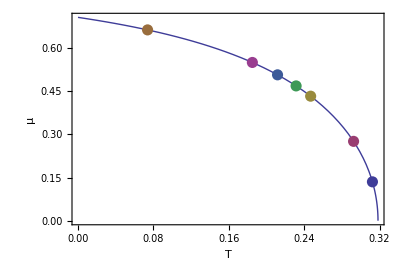

```mathematica
thermoFromNonequilibrium={
{{0.312405,0.135152}},
{{0.292397,0.2759293}},
{{0.24685,0.433013}},
{{0.231414,0.468742}},
{{0.211722,0.507285}},
{{0.185003,0.55029}},
{{0.0738137,0.663528}}
};
Show[{ParametricPlot[{Tt[qt,1],1/Sqrt[uHt[qt,1]] μt[qt,1]},{qt,0,qtExtremal},AspectRatio->2/3,Frame->True,FrameLabel->{"T","μ"}],ListPlot[
thermoFromNonequilibrium,PlotStyle->PointSize[0.02]
]}]
```

Translating qt to q :

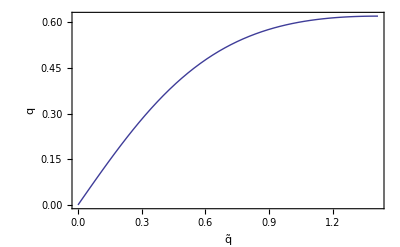

0.620403

```mathematica
qPure[qt_,m_]:=qt (m/(1+qt^2))^(3/4)
Plot[qPure[qt,1],{qt,0,Sqrt[2]},Frame->True,FrameLabel->{"q̃","q"}]
qPureExtremal=Sqrt[2] (m/3)^(3/4)/.{m->1}//N
```

### Examples (spin 2 tensors)

#### Example 1 Comparing the trajectories of the lowest QNM of set 1 as charge is increased with and without scaling the frequency by the horizon value rH (i.e. frequencies in units of rH or of mass density, respectively)

The momentum is vanishing in this example.

```mathematica
qnmRoutine[312/100,-275/100,0,0]
```

{3.11945159116590087332503,-2.746675744340605068091507}

```mathematica
qnmRoutine[312/100,-275/100,1/10,0]
```

{3.121826392643288543956799,-2.745955978739522418781873}

Follow this first QNM frequency at gradually increasing charge density qt, and at zero momentum, k=0 :

```mathematica
tabQNMTemp={};
(* Initialization with guessed value: *)
qnmRoutine[312/100,-275/100,0,0]
(* Changing qt in small steps: *)
For[ss=0,ss<41,ss++,
qtTemp=SetPrecision[Solve[ss/40 qPureExtremal==qPure[qt,1],qt][[1,1,2]],wp];
qnmRoutine[qnmVBC[[1,2]],qnmVBC[[2,2]],0,qtTemp];
tabQNMTemp=Append[tabQNMTemp,{qnmVBC[[1,2]],qnmVBC[[2,2]]}(*/Sqrt[uHt[qtTemp,1]]*)]
(*Keep Sqrt factor commented out in order to obtain frequencies in units of the horizon radius, i.e. ω̃. Remove comment brackets in order to obtain frequencies in units of mass density, i.e. ω. 
Note that the output frequency printed to the screen will not change, only the value of tabQNMTemp will be affected by this factor Sqrt[uHt[qtTemp,1]].*)
]
tabQNMTemp
```

Obtained from qnmRoutine[...] (frequencies are given in units of rH, i.e. these values are ω̃) :

```mathematica
tabFirstQNMRescaled=
{{3.119451591165900873325030189458108541047953815867539181996`25.,-2.746675744340605068091506691198077384198124761804477428831`25.},{3.119268824222886240506809994478086446421832664907672240907`25.,-2.747018941599109993320757530811320169363154435691156622937`25.},{3.118720030958368608295162810265752588758340120511950519001`25.,-2.748051074836916246035185496638523657387259990329841322421`25.},{3.117803740795057261212420014417237825363993719601666333223`25.,-2.749779819047441619885875772120149340111203187579272197215`25.},{3.116517526166319603205695407211902597076591910639323650057`25.,-2.752218136453892081765460660034218048621364263083109760825`25.},{3.114858041100424625558732739842864112796454101610605378625`25.,-2.755384539041752365529956651063314902108193955485752247538`25.},{3.11282108264422855611881153866517072534148380276545304612`25.,-2.759303469850213442534188991686951025904887830503333788462`25.},{3.110401683584045651431957966656024705780138514476388527194`25.,-2.764005817688651903712388967743439529732720843923918586723`25.},{3.107594249014862932369663495605678456132547204121385667009`25.,-2.769529585514765887583562383263743521685418553942308974182`25.},{3.104392754999947846534099721111086818924774784534538542666`25.,-2.77592073943170151732534991674956118847559765175340140151`25.},{3.100791035662688272190272225999376198630828076186367168642`25.,-2.783234273513438946760948743110720206896329423028375808595`25.},{3.096783196778094668074118439197796578846744761281861381248`25.,-2.791535535894824349793935323684076742312229147534278040233`25.},{3.092364211139473665557793906936497235865460580235159129894`25.,-2.800901874252353523437860047001075179473554761053691009506`25.},{3.08753077653861423527211525000043814967715417375078195244`25.,-2.811424674412445780026567762934222161776892423053322574038`25.},{3.082282555611828993313932772467494014657950587001753348012`25.,-2.823211884592855574548412984793200652561287626532763464729`25.},{3.076623975181268703282041627377978066864352707258058023537`25.,-2.836391139272754556361554715918463532745018785939148533084`25.},{3.070566852403847956871230373094556095850135722917818089294`25.,-2.851113618763696276706189152927918997599798138037085994978`25.},{3.064134254211466718334467028019176583900301776498080800591`25.,-2.867558797132818624877354189462585264606571831908911971035`25.},{3.057366214311148350111755628482453583907290676893383109063`25.,-2.88594022725202444403837969946554249133014041268443080902`25.},{3.050328274520288933681138250245470183184769030662153989157`25.,-2.906512452835028393834683544791541860370969014438482397391`25.},{3.043124354974028559095195780299306037517534051672839548848`25.,-2.929578945745544103748240737907813846771865537920237060719`25.},{3.035916289585702335003559659802403030848058851029831633012`25.,-2.955500470977539673657717118642640431664736304586504433555`25.},{3.02895359531194976132081588233434182478343859501739862072`25.,-2.984702106829658949637488503852275695489315702205211120278`25.},{3.022618669476374378886217865710680005244740285206607366882`25.,-3.017674493221955282549450828809077817644472061980704567052`25.},{3.017494048987980221578843045819690041924580375139645169034`25.,-3.054959119187853859508340917371356470531395424301605466214`25.},{3.014456977430583602090388497128934427003519147511575750077`25.,-3.097095688930449436913163093990370010926660840265027289433`25.},{3.014793508173140714038357398746149686500246422806961388957`25.,-3.144488558356887647423035047530557807734814633583373132442`25.},{3.020276766896013372250698113091832718937384356225691442729`25.,-3.197124205616921686183748793418403003845820573165555114263`25.},{3.033035845859319643936837542713639179050929666195743603152`25.,-3.254092162946198676307955378105311715656470863461823129843`25.},{3.054892621958249885870468141074585123177695463441485905327`25.,-3.31308248343735059646767867295999911131934155011938551817`25.},{3.08605083133982704641704704385107813794699379143553745021`25.,-3.370556083160099463521632553957876637574745342406287038689`25.},{3.12408825491000163982083991147630277069812065321014393886`25.,-3.423347341379619929702786358527135460132011700744484910538`25.},{3.164805504278096674976678566919411249498288140762026937839`25.,-3.470840156342596301477268421071301551711548428405038312164`25.},{3.204546698847277327267625622995139480523865535534855870745`25.,-3.515657066981999745392324741844569291108867821715755265468`25.},{3.242079135323140318422635491833513383333797791989307365226`25.,-3.562643452771504761779128649395147611813408366545426368987`25.},{3.279518699999892214985605584836854162451263098182583886343`25.,-3.61727900718975991473707309798692071516603563291706085397`25.},{3.322344626895922624806041140311368818049942203109833687794`25.,-3.683569321212425268078550187665114011234322698081705636012`25.},{3.376649863463973951621577431904790769556467794067971933743`25.,-3.762709743978601520563528539867789741980209531014472444409`25.},{3.447062463064939541749679181689246149269612142889858364903`25.,-3.859238206715177714334408935152904991213825155246124634472`25.},{3.548538922803045910431264055894727729589330678954449899277`25.,-3.991663895674802930907037029437914140061543725603361729665`25.},{3.548538922803019072017304769778898366816308439930458404906`25.,-3.991661471255921981797467128061127214821423147409505590729`25.}};
```

Obtained from multiplying each frequency in tabFirstQNMMultiplied with the corresponding rH=1/Sqrt[uH] :

```mathematica
tabFirstQNMMultiplied=
{{3.119451591165900873325030189458108541047953815867539181996`25.,-2.746675744340605068091506691198077384198124761804477428831`25.},{3.119081189858280309246143262252977196150480355231219038348`24.999947759349507,-2.746853699299483631728915164427727666100584652420447266208`24.999947759349507},{3.117969150987926637415982024641394255167752903723652351977`24.999790999615595,-2.747389439137217841529611320013705006373223989523006546619`24.999790999615595},{3.11611297337517022646241473263163979616615178408689196872`24.99952960694951,-2.748288628928873509300136930282101007368274199227312599269`24.99952960694951},{3.113508501455431928373561591930778473755548797827853942869`24.99916338992116,-2.749560845964487971056096402066428959662104758019848004777`24.99916338992116},{3.110149947991280399427117154054437491311186361981119844458`24.99869207695812,-2.751219788420654390841566619141685016268615243505907383936`24.99869207695812},{3.10602993247747057859434180244506256870340265092289385787`24.998115312682966,-2.753283578657658560827766738240516364469287409482398247104`24.998115312682966},{3.101139542811893031242788989366525165982832089844243899753`24.99743265306816,-2.755775173037964183365906033412881439913954654747095818613`24.99743265306816},{3.095468431506997340840060905775237314954899487899178661689`24.9966435592986,-2.758722894664687002641711686810302795378116474324054933552`24.9966435592986},{3.089004962882897850259741809135646658372829710800954686601`24.995747390198684,-2.76216111085281590174691764038126153376567321566412217618`24.995747390198684},{3.081736435058669155623304127113951877018414786431019312429`24.994743393040643,-2.766131083759834090387682346769133062747814295952606554736`24.994743393040643},{3.073649411256568853056038232219992477160371446371506243308`24.99363069250246,-2.770682030738151931109926062220005296443689089025163847237`24.99363069250246},{3.064730210653160762921594219359099885590419950046981504529`24.9924082774839,-2.775872440954558410996417405415920143002176239483679505257`24.9924082774839},{3.054965632374358342149186237494665274449760166881988326597`24.991074985414297,-2.781771706893907278942273727010151890683517466866078285161`24.991074985414297},{3.044344021336104802320090175043027744441103185714850148719`24.98962948359108,-2.788462143477704293055578357877199907457131451074669993017`24.98962948359108},{3.032856837944286259724222253096777765629264267844587690395`24.988070246966497,-2.796041482879337969853304428267360044519332037498846566949`24.988070246966497},{3.020500975466309986870807785788145260936963991052019620905`24.986395531642785,-2.8046259471273622652891095489567858729553246435854080095`24.986395531642785},{3.007282195584671318835273559033205324331309616391490001874`24.98460334312966,-2.81435400670096737820250706353381046341156793511791571099`24.98460334312966},{2.993220250385635881107121315443594071024422848480640218434`24.98269139814452,-2.825390916265998810351406347448944594675948439167905630379`24.98269139814452},{2.978356568889432119847332361924128952355022666843953377181`24.980657078368868,-2.837934044269884668741450638256441741255096724589557536732`24.980657078368868},{2.962765870215901551886465275300395427042990240465064041093`24.978497374075364,-2.852218806100040774737121452618794838743550714985280929261`24.978497374075364},{2.946573808356086501639530676802236421209757207760113303081`24.976208814852313,-2.868524507161203508442924033356020870070279578877093918311`24.976208814852313},{2.929983839602237504515155905635279599804704182750953548647`24.97378738369057,-2.887178249469681040473338874592343901883961500749043995168`24.97378738369057},{2.913317897352447878869051175550676849654897965621590659521`24.971228409330173,-2.908552507223973808570277096437404806010707296717407427439`24.971228409330173},{2.897076563698785305116126932982604114218827601809584678294`24.96852642978506,-2.933046535825088588378272416039752943675599446123682485732`24.96852642978506},{2.882022684893675468637653018107718769204591351395845525835`24.965675017043072,-2.961030825655399658373680642692727096321067601536037974923`24.965675017043072},{2.869279478181182960026683049510153087615656380538345130344`24.96266654853187,-2.992714580752901811028840588490377936227664850878785994158`24.96266654853187},{2.860388882509538590173603400733855031322085055418703346695`24.959491904129052,-3.027874343829510822055102442588439643028206908896384306507`24.959491904129052},{2.857166213832911281563304810672055428141712011010473660609`24.95614005666788,-3.065404649721235667221816196574624946582410640825071578919`24.95614005666788},{2.861054778960137015328699362118111325399255829579764970995`24.9525975061337,-3.102862079077388848661146926014082383105581374423170607404`24.9525975061337},{2.871893899080916964542538266065512712184086164807056030532`24.94884747755262,-3.136655868864928931900534461473979688109059792240745269406`24.94884747755262},{2.887012673029421704234636167519407408948248092047934789707`24.944868749029187,-3.163562086702078829099519641024378863956742108909167765026`24.944868749029187},{2.902072867613013469723228129884772024550423471028365120446`24.940633876612385,-3.182701443083201791973723842689940851320889058711887195958`24.940633876612385},{2.913223711015481030992427946002938896505589720944983669702`24.93610638537677,-3.196051263979165483745119753378164841762916447069125688345`24.93610638537677},{2.918741726094363861690099610183215558307907185404288362024`24.931236076643067,-3.20733568391589140277170916606892737216979282659320821815`24.931236076643067},{2.91966727023646314558508324541934704240311867520221400621`24.925950624403384,-3.220366185015422227026913350811703550023023544584626221198`24.925950624403384},{2.919443935021046333532339280264198440559224334064749729653`24.920139072849828,-3.236862915118676404584989987496444508849312378264136056979`24.920139072849828},{2.920825147391017817775254221847219160484172731953121979696`24.913614948349352,-3.254769575448809097512258758236527279334333424239970470864`24.913614948349352},{2.922648873747939840918938655477503028419800338891881797646`24.906015684691326,-3.272118889412954420247205686511246564504219714418496312318`24.906015684691326},{2.924370227418354553167048528841650067633105560161395791399`24.896409104142037,-3.28955192779776343902694125367797333668307188595403830694`24.896409104142037}};
```

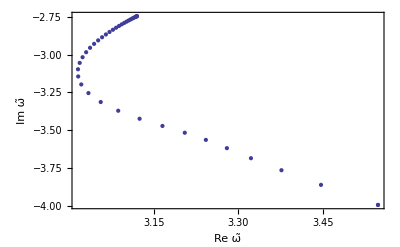

```mathematica
ListPlot[tabFirstQNMRescaled,Frame->True,FrameLabel->{"Re ω̃","Im ω̃"}]
```

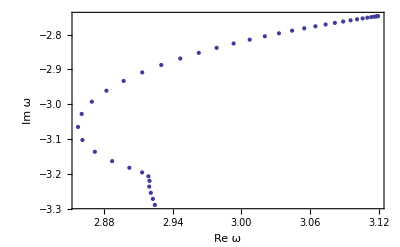

```mathematica
ListPlot[tabFirstQNMMultiplied,Frame->True,FrameLabel->{"Re ω","Im ω"}]
```

#### Example 2 Lowest QNM of set 1 (frequency in units of (πT))

The momentum is vanishing in this example.

```mathematica
qnmRoutine[3,-3,0,0]
```

{3.11945159116590087332503,-2.746675744340605068091504}

```mathematica
tabQNMTemp={};

For[ss=0,ss<40,ss++,
qtTemp=SetPrecision[Solve[ss/40 qPureExtremal==qPure[qt,1],qt][[1,1,2]],wp];
qnmRoutine[qnmVBC[[1,2]],qnmVBC[[2,2]],0,qtTemp];
tabQNMTemp=Append[tabQNMTemp,{qnmVBC[[1,2]],qnmVBC[[2,2]]}*2/(2-qtTemp^2)];
]
```

```mathematica
tabQNM1Ofqk0InPiT={{3.119451591165900873325030215932750388098396209466181874908`25.,-2.746675744340605068091503690568386095995644144539196504595`25.},{3.119644194559368067360955212527323568482772659486301745879`24.999895487269427,-2.747349515679940267209429763463370937772477074462080850083`24.999895487269427},{3.1202234196283945586304846183980293714592738429634872305`24.999581495703183,-2.749375781386254340245845716353666646675263309161410690248`24.999581495703183},{3.121193546615161641653797151889215110906013257166969572698`24.99905665924318,-2.752769493962718880070426604132194344259005051033959062168`24.99905665924318},{3.122561829765565425509401594067290952165038222477286873968`24.99831868118439,-2.757555902678021480243797873095889718019377031346214639455`24.99831868118439},{3.1243386849902827757505601571489279705771275546650428748`24.997364303694997,-2.763771059149438259299166378754779590769214730778260316387`24.997364303694997},{3.126537967032451586895214554081298200478875158110813732181`24.99618926398274,-2.771462551815761760947043311183578563691181509008950320962`24.99618926398274},{3.129177352181139749347388043681992137205550937252787250108`24.994788235880257,-2.780690497840176114731614827629618867533526451714761769066`24.994788235880257},{3.132278849675230027511566368340225901654339498390635164771`24.99315475517355,-2.791528831992061393742163797285411311715702029816914879255`24.99315475517355},{3.135869474409826087306166590552028126438272439119664152713`24.991281126465175,-2.804066945506439913458439482999859624866618870913392795957`24.991281126465175},{3.139982126540164695761101594049500529123647963870441859504`24.989158308717286,-2.818411744710965342036543194216675550027267633237749855185`24.989158308717286},{3.144656741784395429291045256215568489969348499172198787138`24.986775775819215,-2.834690220489273549857288292217751785891038122643302263352`24.986775775819215},{3.149941802237447231547120324003978245392394838728245148534`24.984121347516545,-2.853052646868437239699756987827981853349470591103050840258`24.984121347516545},{3.155896335288460607955105088089876773037292650921512947674`24.9811809847527,-2.873676561975746305087224495506050010536870250089654954961`24.9811809847527},{3.162592583963945098518733826161228594975370651570780109388`24.977938541811668,-2.896771729417230323331123273414605975240582601598964327342`24.977938541811668},{3.170119615457361424970735001745985152048389785587116758187`24.974375465475475,-2.922586334973950956182091933409472250619029548747720156318`24.974375465475475},{3.178588261342900926075772109586743630645461367771780353387`24.970470428531765,-2.951414743913623478444258102331907143928427529960724828564`24.970470428531765},{3.188137978133826543030971960696139046808088907407088032788`24.966198881112028,-2.983607227100290893390361353357258173050210809980258343578`24.966198881112028},{3.198946521118265676443861538766421779197300090909570322346`24.961532498116267,-3.019582151104251933842117130535775482792656937572353692545`24.961532498116267},{3.211243803428218299971558248535484873255383680714823468445`24.95643849380716,-3.059841192083260682311476371595335526840628577234208783805`24.95643849380716},{3.22533206992804325125271739324418965311182732081284523032`24.950878764675338,-3.104988105285540162019047790951302460068971780310202843417`24.950878764675338},{3.241615707368650974491345947062684296044703577109987272944`24.94480880758361,-3.1557512908775422033128851517457219929423344486955838522`24.94480880758361},{3.260645839193972564852026369915236511338666905783560713969`24.938176339979623,-3.213009443568353423342198119876226428910476324614358680178`24.938176339979623},{3.283187454986955963144783626772024005758231299404373595977`24.930919519456495,-3.277817059568679383114081194004593309260599355508461849628`24.930919519456495},{3.310319800779284700780988198174264538257029067878598286276`24.922964616042464,-3.351420582324097497011162331229894202899666348196272556437`24.922964616042464},{3.343581495360015038752626330421834359611129398736439709225`24.91422292391174,-3.4352428687483532976247629176419403892184892633432700918`24.91422292391174},{3.385160631459193481422159341606470567725864297544571061283`24.904586595498436,-3.530788707407647596085902106128467696802745937582406738878`24.904586595498436},{3.438079790008159932264298203202058381637976643649149155308`24.89392291542834,-3.639391011431727921039018347158192322892772272501045081982`24.89392291542834},{3.506189005039212953795257746851676709256567780516682688436`24.882066259423915,-3.761730076049827964202643900936138234609676776734812445271`24.882066259423915},{3.593584826771557403526572287766108741249694626579516954756`24.868806520281705,-3.897303249464525892315022511624208270401035905390076040072`24.868806520281705},{3.70326099760779293957587309168217249536800136087935194451`24.853871964321762,-4.044667299792119884710199337725375729275059336734411908059`24.853871964321762},{3.836043450330778282221849222105001325905330157367691173729`24.83690296741988,-4.203501334018773478897356145798848657337060423712356914176`24.83690296741988},{3.991791644309144274531459158420892810844055937763388919664`24.817410125771126,-4.377795322996117222562748165562113390956519145552729056016`24.817410125771126},{4.172861580113173166843863205890732598050508675135059442683`24.794704094324366,-4.577979877447157357067284895492056169413237318932054851024`24.794704094324366},{4.388127243326231050148043744580847815100429951120850556946`24.76777069553655,-4.822008390552836856466199822021107902617508590047994027707`24.76777069553655},{4.657969932590559120646366360676036889540184371008458613124`24.735030578436696,-5.137698057120846536908527724222370265206361521990820763561`24.735030578436696},{5.023102080686825243972117209236903670469515488563162936029`24.693826047644233,-5.569243049606100385467342717759687902933191593280808616392`24.693826047644233},{5.563611807115692484637920211406882182235957027864079208284`24.639152176308542,-6.199711905241182237086898041530829431964880688164791346546`24.639152176308542},{6.473602476408029725664829134230046319833290407581712284762`24.55971903399547,-7.24767081529070561654019245899633470260438370984225668169`24.55971903399547},{8.530633011002130909435874912478014103646449386003189426366`24.419306567315804,-9.595898632660648811027516270820364941121104349629684576429`24.419306567315804}};
```

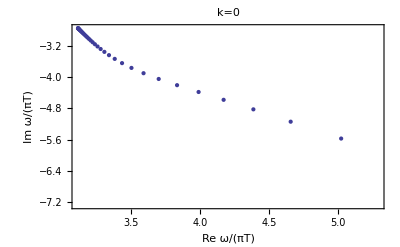

```mathematica
ListPlot[tabQNM1Ofqk0InPiT,Frame->True,FrameLabel->{"Re ω/(πT)","Im ω/(πT)"},PlotLabel->"k=0"]
```

#### Example 3 Momentum k=1/2; lowest QNM of set 1 (frequency in units of mass density)

```mathematica
qnmRoutine[2,-2,1/2,0]
```

{3.177974084931756727935135,-2.729083908524977676497206}

```mathematica
tabQNMTemp={};

For[ss=0,ss<41,ss++,
qtTemp=SetPrecision[Solve[ss/40 qPureExtremal==qPure[qt,1],qt][[1,1,2]],wp];
qnmRoutine[qnmVBC[[1,2]],qnmVBC[[2,2]],1/2,qtTemp];
tabQNMTemp=Append[tabQNMTemp,{qnmVBC[[1,2]],qnmVBC[[2,2]]}/Sqrt[uHt[qtTemp,1]]];
]
```

```mathematica
tabQNM1Ofqkhalf={{3.1779740849317568442898050986883267329272633723562474321667`25.,-2.7290839085249779484396628719433869058733985424055589555626`25.},{3.1776075922226374365744217227874418651947677598277519975156`24.999947759349507,-2.7292542790988116168656511637437520778680334171623447634317`24.999947759349507},{3.1765073068005178500059130845554297930590208269311614774433`24.999790999615595,-2.7297671616939232270917931336947944964130778776787908456028`24.999790999615595},{3.1746708103038599697342763231396160766009139512683424389386`24.999529606949512,-2.730627905959479458821987122675151960828097077804005378137`24.999529606949505},{3.1720940846693427311997606264490563214637593530568231022014`24.99916338992116,-2.7318455527646899537276798321117702468477236187407521203685`24.99916338992116},{3.1687715338229455562553710389892927836508027956999629266005`24.998692076958115,-2.7334330262093311928396271698869515924214028019366399148884`24.998692076958122},{3.1646960201619200016910308114916739914864676589548122995745`24.998115312682962,-2.7354074123588304797532033768283479958658302490038077480645`24.99811531268297},{3.1598589228093249439223460545468497669131832554026836254729`24.99743265306816,-2.7377903352477349538690167829589015163368259152856163538056`24.99743265306816},{3.1542502279954174668033693185858621356358115433756265071768`24.996643559298597,-2.7406084446345202673264402469137478531577237299227754843144`24.996643559298604},{3.1478586665962791389839271896456601988384751380867526518004`24.995747390198677,-2.7438940346848517319490907663777876450735299078730996250865`24.995747390198684},{3.1406719204893255110437043952594025644984921987691497365294`24.99474339304064,-2.7476858184354931021931391220679408217794131085009924929517`24.99474339304064},{3.1326769289326536482829762593851483501487096701043283195887`24.99363069250246,-2.7520298897874382321664961459564919008243315052215169418588`24.99363069250246},{3.1238603400969255323684801542941633524320012753100632074156`24.9924082774839,-2.7569809131150811492351922231008025035174135222480943266395`24.9924082774839},{3.1142091734009652553249861594216047551868340726198524909353`24.991074985414297,-2.7626035904733215523022816746643940547333693522450143519406`24.991074985414297},{3.1037117888642383342954932680590452112173742045380082527117`24.98962948359108,-2.7689744676519972744992447299006858597901946921743145948232`24.98962948359108},{3.0923593056475804430418792509414483755851276739831241101954`24.9880702469665,-2.7761841520643746493695174575041972463850135468815867266431`24.9880702469665},{3.080147681702155557798969418849771302570788754632564027274`24.986395531642778,-2.7843400251569082441504725417671208473120680953674360276237`24.986395531642785},{3.0670807731653975710164762583274871878717441108161582591145`24.984603343129656,-2.7935695337210635835935171662038872399628499174665959075021`24.984603343129656},{3.053174856419066781543701490425757142518301557616930439398`24.982691398144524,-2.8040241248460063889645940519231611485698833887440642047243`24.982691398144514},{3.0384653491264211243923594905119996110281649238092577683751`24.98065707836887,-2.8158838194138085956156402447121849739738610306010660172273`24.98065707836887},{3.0230168552984994179932177970756365676521305302492511064995`24.978497374075367,-2.8293622374582897810676278456199383531005537271968818816858`24.97849737407536},{3.0069382436868827804796681076184197769635263010698277228135`24.976208814852313,-2.8447114652989972742178218334733892108107168969481056398799`24.976208814852313},{2.990405301678892447188680806820933970199525343441442254954`24.973787383690567,-2.8622252170191922650344665526593320862978584790529516392549`24.973787383690574},{2.9736945410555308094203057240714747796267140605091148615589`24.971228409330177,-2.8822367346408320422343300851101496459916469567707185905717`24.971228409330177},{2.9572324989727113642020558117838364080918679227664700816782`24.96852642978506,-2.9051037106434169264410803192506068008128520998112521201114`24.96852642978506},{2.9416635223209070467039631765312568501740511477367033621385`24.965675017043072,-2.9311643711109843211208795653742747726658989230668974037081`24.965675017043072},{2.9279298007054012908294560699396778354860553917004960286391`24.962666548531868,-2.9606348172857316817940602927275422583985831685777510459027`24.962666548531868},{2.9173260075919109826229362888334223133378341991000127624585`24.95949190412906,-2.9934011954241346466721527287813382224770550522571875184165`24.959491904129052},{2.9114146192579246236676658366446053469979967590240847283012`24.956140056667884,-3.028670492869894121771529281571259435927755943405744981453`24.956140056667884},{2.9115824010606015670117377380488954031559315781307123760496`24.952597506133703,-3.0645736415004726295701843399167346538626458079843049325657`24.952597506133692},{2.9180978629980680168372977372802716012950131739275596691369`24.948847477552622,-3.0981565476351360253331991929105657667232156286085083543866`24.948847477552615},{2.9291787888796348731531055854269546909336332802379874562492`24.944868749029187,-3.1263778806898112474926356958614513399672546313075055185424`24.94486874902918},{2.9412523009122974677221982111798298261020340254976329938121`24.940633876612385,-3.1478282859299571855806008947952554269405730615821841562642`24.940633876612385},{2.9506213154015285324333574087246390156407912821141938952947`24.936106385376775,-3.1636561641593338382201081332517370540501417340740034451496`24.936106385376767},{2.9551998659432056047263158260936498611026188648879821609693`24.93123607664307,-3.176965451332064081091973998769785780050272933970710398531`24.931236076643064},{2.9554344450389149725873078172552175286254910029556119241588`24.925950624403384,-3.1913302581722200931078232743742381946179497576002135676542`24.925950624403384},{2.9541755149185609427298176489885051607035364282783250421946`24.92013907284983,-3.2086942386707597157095888223725189125018375828689927379366`24.92013907284983},{2.9540370272103950176601671569768211304163147869767946966609`24.913614948349355,-3.2275950447935455667260621567298339436516574206643471663924`24.913614948349355},{2.9541672294987817230036377587045825789032267927653946320857`24.906015684691326,-3.2462452196328379830801887979045792322350426432577591738779`24.906015684691326},{2.9538057157191482044168004762949408759341578661670397334947`24.89640910414204,-3.2652933113737372257710814085363506486149105917657909612129`24.896409104142034},{2.7234464060120030578336908160716705702472677962746131270656`24.875061263896775,-3.0106419275008882357961197288816388752500364048315443033772`24.875061263896765}};
```

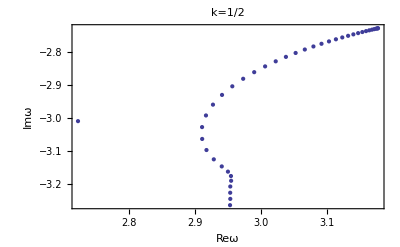

```mathematica
ListPlot[tabQNM1Ofqkhalf,Frame->True,FrameLabel->{"Reω","Imω"},PlotLabel->"k=1/2"]
```

#### Example 4 Following the second QNM of set 1 along a charge trajectory (frequency in units of mass density)

Zero momentum

```mathematica
qnmRoutine[5,-5,0,0]
```

{5.169520975761926874725122,-4.763570116921526917429108}

```mathematica
tabQNMTemp={};

For[ss=0,ss<39,ss++,
qtTemp=SetPrecision[Solve[ss/40 qPureExtremal==qPure[qt,1],qt][[1,1,2]],wp];
Print[Tt[qtTemp,1]];
Print[μt[qtTemp,1]];
qnmRoutine[qnmVBC[[1,2]],qnmVBC[[2,2]],0,qtTemp];
tabQNMTemp=Append[tabQNMTemp,{qnmVBC[[1,2]],qnmVBC[[2,2]]}/Sqrt[uHt[qtTemp,1]]];
]
```

```mathematica
tabQNM2Ofqkzero=
{{5.1695209757618614414618326841224594585591672523509365312569`25.,-4.7635701169215653002553552329746205432507706745979163824905`25.},{5.1688204569459255607337177890427155878341037500710592506645`24.999947759349507,-4.7639556670559642934323423074808178263158946682795639595729`24.999947759349507},{5.1667174474258834017357141844200019935397143595096080841554`24.999790999615588,-4.7651172295670393162942773937273167013385875045029102482641`24.999790999615595},{5.1632076253919686705663024826169143415890160054440170573235`24.999529606949505,-4.7670696693850627053260410623666718277355709087613059528335`24.999529606949505},{5.1582839179397587325524511895803169366443858173874709153286`24.99916338992116,-4.7698381957380749262811207902811659264572032582605787667906`24.99916338992116},{5.1519367159735845155098295288840860655852122323579696952483`24.998692076958122,-4.7734590337540884437373596640002267640982564526620815170419`24.998692076958115},{5.1441542174046732651195835656980662348206907814861244414362`24.998115312682962,-4.7779804059191651686294348055967878531692515282057366312514`24.99811531268297},{5.1349229481671359557924680248609918314320190520744895189171`24.99743265306816,-4.7834638670019312235902996718330437801086597849667584405198`24.99743265306816},{5.1242285364208511751317987621947832355440724376903148704748`24.996643559298597,-4.7899860517781511269496892820156793065050569487547131626532`24.996643559298604},{5.1120568527519295219397982584768942264357170011669507290791`24.995747390198684,-4.7976409125839264199233266056634945515679672150321903259109`24.995747390198684},{5.0983956846693359320264675059170134525298963995172464315347`24.99474339304064,-4.8065425427955741517314644262798486052118480997677495169026`24.99474339304064},{5.08323719722164889736859760460208725950950399674313546521`24.99363069250246,-4.8168287005312292416468021307544170329270929276244727377239`24.99363069250246},{5.066581558720217021755195793834852800568489101292400176367`24.9924082774839,-4.8286651583459155040846347846631257816987508582116566167954`24.9924082774839},{5.0484423056886060730771878906619797072634386600373743254777`24.991074985414297,-4.8422509959044001297873652688682491977491629492707793793782`24.991074985414297},{5.0288543217273219681029487729589267293610824249416155623665`24.98962948359108,-4.8578248937483428793736024718355559824533546837203551840288`24.98962948359108},{5.0078857666354628590566297316412082083416881935557331646407`24.98807024696649,-4.8756723132990897166561679442397204124916963824177203320486`24.98807024696649},{4.9856559906056264206489204624699778191238554178282510544092`24.986395531642785,-4.8961330255828799346828025851643165982299655844649937176096`24.986395531642785},{4.9623624837166180528118543416728253389762167336851803922365`24.984603343129663,-4.9196074952675810245564623284564070233693841844046450182669`24.984603343129656},{4.9383212471211909631261497147002220556051259675291142486203`24.982691398144514,-4.9465585559930654127106137707172541263384196729380237861785`24.982691398144524},{4.9140262693675536077200903933733618709846177234519676385132`24.980657078368864,-4.9775004855967435908837428092625888503210901848598875825358`24.980657078368864},{4.8902334437751340126809860735074412711369189569733214923683`24.97849737407536,-5.012958985085942483866634068150699686671348732565795768014`24.978497374075367},{4.8680670578023586806503676213018577036455309103279519436045`24.976208814852313,-5.0533700719776569779970059637117432068002063163747615359458`24.976208814852313},{4.8491191611620299568027128597254207821676916067976087758997`24.973787383690567,-5.0988643239662593664748715922161070225100869503857903232516`24.973787383690567},{4.8354376276765349141154189712527197990260801263931393945002`24.97122840933017,-5.1488768805400579605572750948130698659959732172175004518831`24.971228409330177},{4.8291686080541964993650270814617463814320288946054649544798`24.96852642978506,-5.2016175081940734244772432188736752551388128435638585660447`24.96852642978506},{4.8315881591442113863040047675115817517813538177304630826785`24.965675017043072,-5.2537711296313510898737016969380886818041017742324081196493`24.965675017043072},{4.8417865268053855495795817083364124808995558891767385848731`24.962666548531868,-5.301202315589320155192201409532069674020043004668396821842`24.962666548531868},{4.8562885059715782799546774686704507266730141768745592141208`24.959491904129052,-5.3408718034734494081768734871962217231282221348476131227791`24.95949190412906},{4.8705304947575572175106631641038375173378876525642245081987`24.956140056667884,-5.3724686398335818961935506974108432477967502488799206921098`24.956140056667884},{4.8809651057376939102284561938796827885800856982714044692702`24.952597506133703,-5.3982366827473904796816613593415068998922554172601786651045`24.952597506133692},{4.8861333612455701118350027323794104145655796899242260155156`24.948847477552615,-5.4215820482979651038176038559967187429798772347094166552781`24.948847477552615},{4.8866476534383899544300196510470335870382404675327735176836`24.944868749029187,-5.4457161397016846229740247880640158481927427913852043095996`24.944868749029187},{4.8846541545447232444618188300003518177630310134428532179672`24.940633876612385,-5.4726329921171530574763285610831848707181614287172148401522`24.940633876612385},{4.8827623872664412459180084901378124712502074811156684507335`24.936106385376775,-5.5023672039699310906383300159560734782225643578185570964392`24.936106385376775},{4.8823651259114077923238651028852138984307673511710118144706`24.931236076643064,-5.5332433511109883700880909031008312646982199586023180705315`24.931236076643064},{4.8828599692070939844110585452524925688511111636712559670561`24.925950624403384,-5.5638174890481114481482421865539876122339645287577147846634`24.925950624403384},{4.883391972831648840523727185568396747081437315876718537754`24.92013907284983,-5.5942441478840554797153906774340545338211065941812413870792`24.92013907284983},{4.8840937084897672651251329126259984297627204588869001263837`24.913614948349355,-5.6248421679185279346091654233287104982096376543172578256732`24.913614948349345},{4.8850477256927845145397961902891675425045367273641664327818`24.906015684691326,-5.6555507276933431873012125823427203345676504368410005269259`24.906015684691326}};
```

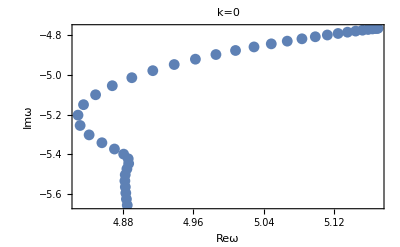

```mathematica
ListPlot[tabQNM2Ofqkzero,Frame->True,FrameLabel->{"Reω","Imω"},PlotLabel->"k=0"]
```

#### Example 5 Following the third QNM of set 1 along a charge trajectory (frequency in units of mass density)

Zero momentum

```mathematica
qnmRoutine[7,-7,0,0]
```

{7.187930826321584211467166,-6.769564908542766312772079}

```mathematica
tabQNMTemp={};

For[ss=0,ss<39,ss++,
qtTemp=SetPrecision[Solve[ss/40 qPureExtremal==qPure[qt,1],qt][[1,1,2]],wp];
Print[Tt[qtTemp,1]];
Print[μt[qtTemp,1]];
qnmRoutine[qnmVBC[[1,2]],qnmVBC[[2,2]],qtTemp];
tabQNMTemp=Append[tabQNMTemp,{qnmVBC[[1,2]],qnmVBC[[2,2]]}/Sqrt[uHt[qtTemp,1]]];
]
```

```mathematica
tabQNM3Ofqkzero=
{{7.1879308263222450849420155161252002672181616393543345014952`25.,-6.7695649085432580144519652679940128030597433264101498149127`25.},{7.1869013707442761116677011529319152068165344622798545165128`24.999947759349507,-6.7701764113561462097612017423134431837963056983869575870285`24.999947759349507},{7.1838110796224477157944262677656790180810653897860666839644`24.999790999615602,-6.772019674154411161326152738495731453503342213705270908875`24.999790999615595},{7.1786542852786716998979272299076271877900204085795224046162`24.999529606949505,-6.7751212240373339939451285559931337607203315696120798110389`24.999529606949512},{7.1714219091041747547069325206011020380168981396279270527707`24.99916338992116,-6.7795261658447462027831805757589892243137119997314945420014`24.99916338992116},{7.1621020710832938466563896553928210825051219237972879491747`24.998692076958115,-6.7852995675139951167453174961425932170284787010157822708147`24.998692076958115},{7.1506810694303457268251435295662301866282220955262771778073`24.99811531268297,-6.7925284931481275745191829009463362467485236023451287308256`24.99811531268297},{7.1371448815880893078761842728933793616014938830004403563736`24.99743265306816,-6.8013247811695658836702738190693465549597869742905353077983`24.99743265306816},{7.1214814223893060929127024498495749254563099117990779804323`24.996643559298604,-6.8118286962752907622966266947918989913539430891879473249934`24.996643559298604},{7.1036839221393098513213913111500967449697917386962044351423`24.995747390198684,-6.8242136130762145281051552163458225071452859221793630041957`24.995747390198694},{7.0837559819263724300430448828554985338922367281867662423925`24.994743393040647,-6.8386919066325013243904431379913548888832890153719658135194`24.99474339304064},{7.061719165061102323471609015348590403109265010401496580003`24.99363069250246,-6.8555222074971543447600281981485122756994894804852770792251`24.99363069250246},{7.0376244530068450177516960518361067034165847619358230479129`24.992408277483907,-6.8750180743074729271220833705583716964288801202559975876144`24.9924082774839},{7.011569620864864479551590059773423079690821157258610038577`24.991074985414297,-6.8975578313720842515599216595198765844236520204778059355448`24.991074985414297},{6.9837256873501659947445227630511101499995010183639942676418`24.98962948359108,-6.9235945664198540132944062143401943256222399135052499173063`24.98962948359108},{6.9543771647320053259225149422277258334809251532718665665482`24.98807024696649,-6.9536635646517233947451467932159900597167299724176395951551`24.9880702469665},{6.923982757588521498059371997567583350376954747620359571202`24.986395531642785,-6.9883807016421613969837523230987780448867725355362899037134`24.986395531642785},{6.893264433288139484633827952015249444300662215114096862158`24.984603343129656,-7.0284174803216395623536167908286390978059258615492578294585`24.984603343129656},{6.8633295552650909966293997251660724307615505804038664695798`24.982691398144524,-7.0744231745806282991448743622923811555860040576937884388452`24.982691398144524},{6.8358114731604939482901997051571791380185902577505482642015`24.980657078368864,-7.1268393505650415825724871555665610908249236254310999068348`24.980657078368864},{6.812951723774245182035774271059393612712003525003810613892`24.97849737407536,-7.1855273147436475879296167613772807610014537098410933238445`24.978497374075367},{6.7974083000259120615803980363846961301533190254777718713325`24.976208814852313,-7.2491688392772830457702079355309576270122047563002321886916`24.976208814852313},{6.7914284984355339791133009950608639127384835045420410086945`24.973787383690574,-7.3146730671327517356960036194913819761185096114366049287461`24.973787383690567},{6.795308775296792120845999620077567222200570666697531053884`24.971228409330177,-7.3773876606004331191846613882580476663099477555334422772818`24.971228409330177},{6.8062390432194702469865234829530736868377064818136969317686`24.96852642978506,-7.4329038774423774418522513091440528611622741944904647383975`24.96852642978506},{6.8192216695256199031414987217889398618340033480371301967954`24.965675017043072,-7.4794515681804019044827009233295660076453693341121827105577`24.965675017043072},{6.8295989448977008963921332315439363902566140999800233802796`24.962666548531868,-7.5185511192762639551275497806313928430077695234072948868636`24.962666548531875},{6.834859275676318800954869973066980476967890983009740317589`24.959491904129052,-7.5536385837635315025309910315365128271370070766979899135855`24.959491904129052},{6.8348715857585565501964159093029857701240448070138903616369`24.956140056667877,-7.5883280883682057197459633627067267824668090007591444728182`24.956140056667877},{6.8312792260607369613094282715391160921498068130328151444405`24.952597506133703,-7.625238581050918440733808210449763467250786139112666465047`24.952597506133692},{6.8265675566451295390980502593460237784864781165418140930978`24.948847477552615,-7.6653216470508509627045308404944613141016221942870103688888`24.948847477552622},{6.8228206477452464916559443406075207354260698104759532498267`24.944868749029187,-7.7077655092913036835181915589152512128625389661991021198553`24.944868749029187},{6.8206160292447941332247081688631990165664793685984113260155`24.940633876612385,-7.7509309684246920456480713831039107816512624092308632302411`24.940633876612385},{6.8192280388399138188101619676409032981068741984122757018314`24.936106385376767,-7.7939058934730967525229593129031688800015851452378858274074`24.936106385376767},{6.818067445844109627733190131956139728991055957247526433007`24.931236076643064,-7.8368904368076943537383284206198677238412924814311183996356`24.931236076643064},{6.817238356840100278163773119037913489699133660589031075868`24.925950624403384,-7.8801276886094143660027026082844975286264672148396031600498`24.925950624403384},{6.8168575379622748430438803892763131204633370650795616578101`24.92013907284982,-7.9235364464518647271681317787437414269944269055320479000506`24.92013907284983},{6.8171012999027341788361366262768774475101961200948083344967`24.913614948349355,-7.9683584372192921997796446757310110460150205507325991457062`24.913614948349345}};
```

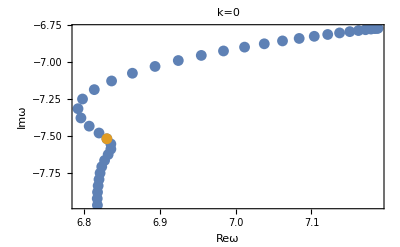

```mathematica
ListPlot[{tabQNM3Ofqkzero,{tabQNM3Ofqkzero[[27]]}},Frame->True,FrameLabel->{"Reω","Imω"},PlotLabel->"k=0"]
```

#### Example 6 Following the lowest QNM of set 1 along a momentum trajectory (frequency in units of mass density)

Zero charge

```mathematica
kkGlobal=0;
qnmRoutine[2,-2,0,0]
```

{3.119451591165900962536045,-2.746675744340605352172666}

```mathematica
tabQNMTemp={};
qtTemp=SetPrecision[Solve[0 qPureExtremal==qPure[qt,1],qt][[1,1,2]],wp]

For[ss=0,ss<201,ss++,
kkGlobal=ss/10;
qnmRoutine[qnmVBC[[1,2]],qnmVBC[[2,2]],qtTemp];
tabQNMTemp=Append[tabQNMTemp,{qnmVBC[[1,2]],qnmVBC[[2,2]]}/Sqrt[uHt[qtTemp,1]]];
]
Clear[qtTemp];
```

```mathematica
tabQNM1Ofkqzero={{3.119451591165900962536045166768147246326173260025705122836`25.,-2.7466757443406053521726659683884899852507497582399507332254`25.},{3.1218263926432886343002964907982503407387374646947742833937`25.,-2.7459559787395227024181808913874739693326523144766238633209`25.},{3.1289334263732014803024553900335737917527985135214412095389`25.,-2.7438049217527481381750954566943789569798618646167500022367`25.},{3.1407211934306116820576130238673759696512134997677304595302`25.,-2.7402470107056685250143914837694096882234908517973155845135`25.},{3.1571058586436322674340315591247028080879614964146114745103`25.,-2.7353220530407284325216290774197026021965990733254273829524`25.},{3.1779740849317568442898050988091726034822937775164669192251`25.,-2.7290839085249779484396628716837472446200834806873236638929`25.},{3.2031867023024862404884127957166499627215257109819688531781`25.,-2.7215987659196765928928000841710202404450515397586180190468`25.},{3.2325829580609947585674300046347678868366327079571377879897`25.,-2.7129431201770299372860639481579249877713256973371813554168`25.},{3.2659850778946101211650582316477101556479661573604629149957`25.,-2.7032015670496130070974980060035042137402177818603581702406`25.},{3.303202878035366688380280143667525116156026082116718436678`25.,-2.692464532293864514118727020830000978029758507007191214879`25.},{3.3440382014489154673382021781047738179207028604489005631956`25.,-2.6808260435913342589465379353759508809173336537001935272663`25.},{3.3882889984533172513699825793430789572684504517622781212588`25.,-2.6683816370437797943543112592277485583397828760857406035995`25.},{3.4357529262838619090305936347772116257467920707435720868286`25.,-2.6552264692833242131113801517128820930590945631111955929113`25.},{3.48623039570765645973118752890316817459476294570893942624`25.,-2.6414536835980578531438449474596917095199922826150210259481`25.},{3.5395270404530214907057692292392562821865669226643805201051`25.,-2.6271530564073841674178278247419877230932972330692564816125`25.},{3.5954556236751296222363650473895468194743023499822496819262`25.,-2.6124099307631725425139708385127607028542122504292770285427`25.},{3.6538374236478488722507927641973494444042923326461486606494`25.,-2.5973044274657574982994491137952576151979980644119083907389`25.},{3.7145031586441521669701327067613230636133564686203871233125`25.,-2.5819109123844710003621467544667944402945987736733323721347`25.},{3.7772935198741328832082821237014853625902501795114873922271`25.,-2.5662976906394633746732740551254074240371502952234467100085`25.},{3.8420593832466753754233773614850892161832414480213365305901`25.,-2.5505268940284012565235203685189257692180329168936794291693`25.},{3.9086617675808395071867059072815509014336792177665140299377`25.,-2.5346545268341282536183501006091381238589661610242186839219`25.},{3.976971600529275137616392991181880903243252285473475165348`25.,-2.5187306362036945476515600312374334244327322334572621641649`25.},{4.0468693453916388253793374989032973420205869805574624611992`25.,-2.5027995759357334694727582542601446710561083271510911576026`25.},{4.1182445333318972479887359157260912344005488905152343462128`25.,-2.4869003361239979968670238198153304716285219735828815640943`25.},{4.1909952370619603792955686007458918482017260161084240489184`25.,-2.4710669151681554801763006181548022929350187673113069952615`25.},{4.2650275143097409590758575863545493092421450609495162970476`25.,-2.4553287147923929158927992925424772862561281731791086245125`25.},{4.3402548426139030015047032828734541279908736082316383005842`25.,-2.4397109426396740768097684622734169851540327620604568916384`25.},{4.4165975612733092689435348440390700592210339315218256489313`25.,-2.4242350105671145828189922917101129154319929186543342534279`25.},{4.4939823316076285705651180111533835395518750175426684906235`25.,-2.4089189198683090590395342304316756725138217077544788898869`25.},{4.5723416229707602860284661976555801849961685126155637048114`25.,-2.3937776272630034759575321065049200805521561175510197523789`25.},{4.6516132290807321068634422095311566257206256705166783657456`25.,-2.3788233876351986915635111316148826602884994773167640686345`25.},{4.7317398170573259749690838035515003807677121934960243873737`25.,-2.3640660712048446946992322711075010511103566223937108452609`25.},{4.8126685099638406632018111298941302206833403682728265220388`25.,-2.3495134541366513457831488372413768714606922846395080905753`25.},{4.8943505025154336628209611756857945735373937026557727395038`25.,-2.3351714825784068363074570245752681445057126767493496122136`25.},{4.9767407088419843540328010873421432166275089162730334758513`25.,-2.3210445108364310019798131081730404179205404813084564524302`25.},{5.0597974406932820769290902985679486947421374530493157277611`25.,-2.3071355148894563013382080532064397921015255573746488927274`25.},{5.143482114179122518650154983431205123861516898486637148154`25.,-2.2934462827606871076181916863756350415762203957006821952504`25.},{5.2277589829912361334740730256607818062394711667785441838661`25.,-2.2799775834509333531703934339214843632015582938009405219621`25.},{5.312594896014638246064874950839790096889673295107982590293`25.,-2.2667293162169378075542733956776395359858461745122410289615`25.},{5.3979590772698428494876207899831817970683052936121842658353`25.,-2.2537006419856099678949822380809865169464192232625781768243`25.},{5.4838229262094747968619594649259486580045280298566346080812`25.,-2.2408900986486842080635680809870078219223786055369998111621`25.},{5.5701598365047106828183610513447205831780222746066091278647`25.,-2.2282957019004678944160013276209904026515178891132070162892`25.},{5.6569450315853162669288769794621891446773724567644808995038`25.,-2.2159150331770127162111941906848170415347769299512564059476`25.},{5.744155415332361162261789982126037742456740495887755608813`25.,-2.2037453161381550347927360553508538626367229455136526850889`25.},{5.831769436458454396144247009922851274103937662292234485962`25.,-2.1917834830117351346562940994667406375159937338577606773863`25.},{5.9197669652422199260915989529165002687109000159262193239945`25.,-2.180026231997154174978673292644054383529215302023003779052`25.},{6.0081291814089835074273074658001153964729566658513536107652`25.,-2.1684700768068809985187907172705969735799356325461296417536`25.},{6.0968384720666878321849019983484159333136709868607860787838`25.,-2.1571113893119621747783385147749932668441190621926321346433`25.},{6.1858783387141226218205431630366784243356253777820889631351`25.,-2.1459464361524755764478659817247924407415540433855462944123`25.},{6.275233312437435991795473318061930799774686070101556546758`25.,-2.1349714100769626946621419076598862309094575043581149371363`25.},{6.3648888765007496458415737596060226152687448829251345258301`25.,-2.1241824566864629216399808170010144769813502210789800637149`25.},{6.454831395617927602804709116828726504643301982461729926513`25.,-2.1135756971787714753820114344540144985576047650600568529152`25.},{6.545048051265689110832479001388340946080816328719553036258`25.,-2.103147247616652040546228179815281477799921446328232008707`25.},{6.6355267824639219927873136700500554489563116846851768891234`25.,-2.0928932351794964418606779127755788654266404759353702719302`25.},{6.7262562315078815023032798235445553581427708726118888977839`25.,-2.0828098118007940236793017271631777420383341862167946498225`25.},{6.8172256941895849430407180252270832561073366693870998864428`25.,-2.0728931655431673354317051382429079770266439254537832797517`25.},{6.9084250740927420528971257784055126245586767610448251160495`25.,-2.063139530018052722345351234367808916704016900516220076838`25.},{6.9998448405875669600347587707201170570878271501799633074677`25.,-2.0535451921177708876598365942874805882785963753170416409217`25.},{7.0914759901893277587398714167350734099180935718832741971978`25.,-2.0441064982931863133586091807158981010424489911699662256414`25.},{7.1833100109779882292739456316913424696390385439424248757261`25.,-2.0348198595798729318626406367362001213204070135331104119403`25.},{7.2753388498062168633102528485755855491332086358481794671977`25.,-2.0256817555492073196749804111445026043447108315758614424313`25.},{7.3675548820497830205391770121024232357179385653676549756039`25.,-2.0166887373376541954015475230802052677170517471392984438631`25.},{7.4599508836782685936241564830295646650160110084700995002794`25.,-2.0078374298873028220804303814620824766813255876999390778145`25.},{7.5525200054454228764711462846167058175928944087147397936031`25.,-1.999124533513091438012411689759605141766429810001288218561`25.},{7.64525574901764939777077412027150699954400762398444483923`25.,-1.9905468248968065988247770295468498104392235549996763452431`25.},{7.7381519448762879932848508443756009396644302809928336463002`25.,-1.9821011575945798987026846380809447316749713094812084852068`25.},{7.8312027318447623346764095949961796128555738702950453229132`25.,-1.9737844621329759526160475927177492754777189959976813443226`25.},{7.9244025381054971353893157571635484417363312462945786593802`25.,-1.965593745758652047634917291251385352636399122732698570105`25.},{8.0177460635839428176132516679576816446137201692005759554385`25.,-1.9575260918977773376692376985067367696498956104960558287692`25.},{8.1112282635882308279880655927160707581106167923521878186058`25.,-1.9495786593737578362353364233734260294672554448015471852286`25.},{8.2048443336030551003467720666971507065604469537494027567066`25.,-1.9417486814251738252564205060079704449842919915792431394255`25.},{8.2985896951454538305368276475687407827098679001374810239798`25.,-1.9340334645600685529437685650363878333653771686711198740247`25.},{8.3924599825983565668752042650059322032054815719388182516797`25.,-1.9264303872777178075873970426511365662928246045194656306013`25.},{8.4864510309451584600038726062383900446525799129289928693697`25.,-1.9189368986846601842451300766621084587138705892337070840587`25.},{8.5805588643352695720287328447876724155122063745223788646447`25.,-1.9115505170279915016803010925790867295953744689995016386545`25.},{8.6747796854166362692629688754951927345052527533011010327329`25.,-1.904268828165648954284629124722246141978713813125902415126`25.},{8.7691098653767096040395559733421491764907158589884604236523`25.,-1.8970894839905660029400340768779420182992668405257449605613`25.},{8.8635459346383001566395220196470100439378529624627302783356`25.,-1.8900102008231113338556418539390637945984019453652430920193`25.},{8.9580845741612656921903548559698936762464803244909253649738`25.,-1.8830287577840831296808961451520912042228682455630517550662`25.},{9.0527226073050590004349914648044278950729637422758652058585`25.,-1.8761429951586786217973214177888954476155247012162713250522`25.},{9.1474569922108937189763103577879166675807351984195460058431`25.,-1.8693508127602431009829033360905302418239905595353232563363`25.},{9.2422848146656514517940595654754007717482983775156151482049`25.,-1.8626501683012164396724844698114523058781764567900556942773`25.},{9.3372032814127385511165738331614948931689680842382820750609`25.,-1.8560390757774849258653100591003322885394994680897258935161`25.},{9.4322097138779005948939244355617162993956076687857554133059`25.,-1.8495156038713040527398402623155342180306700648104756193681`25.},{9.527301542280557960354013003526536221336672655458096217592`25.,-1.8430778743770558242321662901702408987695333535992863358349`25.},{9.6224763001035571606852922963518408768248292629012294501847`25.,-1.8367240606533252247031572094434505544406397674608768832486`25.},{9.7177316188963612972424258529255679335380119227208817850391`25.,-1.8304523861041086718237955617742951269459663895806320315118`25.},{9.813065223388647917623077621266956117114603332037373651243`25.,-1.8242611226913886473373681038338622733366706524740246932959`25.},{9.9084749268930617009263459169913793553264401397154290441949`25.,-1.8181485894808108250686512973837544145431450698188915481406`25.},{10.0039586269774968952897227621209683617637117566005503569847`25.,-1.812113151221772872358143394525265154432609023540720224185`25.},{10.0995143013887755841272321315594395769696916318330395353026`25.,-1.8061532169628678915076164275767608290098626397312496865338`25.},{10.1951400042109539703682275490798642874696365917475019155753`25.,-1.8002672387033127783106105360998452629795417511926178023843`25.},{10.2908338622427420110459694391237723327241268961527019103779`25.,-1.7944537100807251783997540906211096900974325883865731596098`25.},{10.3865940715796717511520563821451485621132261652310113809716`25.,-1.788711165095386437934318493747493964248965997522294184504`25.},{10.4824188943877059017401250588368751098790070925743960247085`25.,-1.783038176870936498582549322114220077523160814054040255127`25.},{10.5783066558559487958155762009384186860506423204328584239114`25.,-1.7774333564512856536878939281076182250792281105042320582783`25.},{10.6742557413170145539316899420423133133389771677838169402203`25.,-1.7718953516333932669016026896889190542678274438543156972704`25.},{10.7702645935244286731202493799805584895979178404412199925582`25.,-1.766422845835451582602697207720877924531915671029339320996`25.},{10.8663317100771957530875959405853871850946391714211503275938`25.,-1.7610145569999204538135559896857932181825891267088126305916`25.},{10.9624556409823629710000973801766095076654926198896555802739`25.,-1.7556692365307837148820023165369525933774165466360338867116`25.},{11.058634986347051686629315191957690077178991920533617918114`25.,-1.7503856682643374286766608120111992677883943276156372113255`25.},{11.1548683941920224303927955234981817320204212504646292478111`25.,-1.7451626674727725370675166312375865634618127521934024886021`25.},{11.2511545583793859010041369964420025945239633679472501141254`25.,-1.7399990798997777920360461128737126127296847409774071455471`25.},{11.3474922166475781817620915291190762072571477656800950603474`25.,-1.7348937808273615242786931151158092943434856875430471538931`25.},{11.4438801487471862196705428606826289334069483282050046997955`25.,-1.729845674173071141650937671853114402521681164740976427177`25.},{11.5403171746716409434209788352143066772300776499164156804339`25.,-1.7248536916167779573427772457589671756153170278615906897216`25.},{11.6368021529771966061768304262267967897347571875817691593007`25.,-1.7199167917561871694104703410046442297065757573276796077742`25.},{11.7333339791869845002958458780127019706869911229013002282324`25.,-1.7150339592902323760270935822901441913869393593808574913337`25.},{11.8299115842742727288845447969017310920493493406301318496561`25.,-1.7102042042295164960463288068010936273879643785006851395941`25.},{11.9265339332203820425286741370623363304373942915810976056735`25.,-1.7054265611329670051098574832543992240085959132659836524297`25.},{12.0232000236430025282281359934771190229205413250409298581738`25.,-1.7007000883698832606590168536690942273639743699038089279042`25.},{12.1199088844909302453909487729758195053382890689535426818284`25.,-1.6960238674065649259185723663569088374867670944973515252404`25.},{12.216659574801496933620850914973873877892651732695567670948`25.,-1.6913970021167247524332840615593079800175432956669179496731`25.},{12.3134511825172024259924021095297980266107639377161414951719`25.,-1.6868186181149041809194960364885710421769293779405674509386`25.},{12.4102828233582792893717895221418514670978369581434223219362`25.,-1.6822878621121268125993853229596932689295536247775124204856`25.},{12.5071536397481230213039286326540819002565596805058005539002`25.,-1.6778039012930431954419231197312546489251187103966090444737`25.},{12.6040627997887119179442553444835133638317620801019412648088`25.,-1.6733659227138382860713697348985069832985528690787586528707`25.},{12.7010094962833176400445784190685986758489469212768157025721`25.,-1.6689731327201922099997757205385991244701607201435789532382`25.},{12.7979929458039719916860227060735178881866722567884913880226`25.,-1.6646247563846051419109044356470549258585989313583345132027`25.},{12.8950123878013100643152104873292352619226939088138504273047`25.,-1.660320036962415763463521068254994980467372472403682663982`25.},{12.9920670837545524975468708574465661829192126280773164702666`25.,-1.6560582353658636545290692694528528388583031705646762910543`25.},{13.0891563163595238493838576483863840897356099218532915157408`25.,-1.6518386296555652461735577697178861612712961789850809999499`25.},{13.1862793887527288230030785625614163989102881480757111657506`25.,-1.6476605145487928848951286213710856747261259054678621736884`25.},{13.2834356237696246564816361251460261839049083274217023166158`25.,-1.6435232009439662253365055276449674111769863351869209265461`25.},{13.380624363235337163991620930476723083862696012493226028854`25.,-1.6394260154607843383330556181254672461624551408053259669989`25.},{13.4778449672861696053545283737290853317121260334712995620055`25.,-1.6353682999954460010814712915070738947782038709742927694186`25.},{13.5750968137203489305879530570955707083717725947334594761909`25.,-1.6313494112904244144616790747837415440544130734134064373308`25.},{13.6723792973765431460649899370371501246238171746158247539284`25.,-1.6273687205182806474461062229200934606051110560315164972774`25.},{13.7696918295387669771405966049696873862173376346233557001178`25.,-1.6234256128790181984800714890998526824705900085894813769979`25.},{13.8670338373663710650058347169877562257080425695960145437985`25.,-1.6195194872104984414536091331375853625565696755520450248655`25.},{13.9644047633478835814176021773263029286899865831953848022151`25.,-1.6156497556114535118085333709239202880307341553201634826167`25.},{14.0618040647775411110068511723286368372610762700193063618602`25.,-1.6118158430766500983407311379249964615747442677226306244384`25.},{14.1592312132534108861217191155874128900473221988196928136331`25.,-1.6080171871437730883996447549308340420501011328954297301151`25.},{14.2566856941960661593122252940695046091985985413278819657747`25.,-1.6042532375516143379369832697650384447963917711802308155973`25.},{14.3541670063868336662944367475989007264007978597781594842182`25.,-1.6005234559091660014085743042991761563407745664488726004356`25.},{14.45167466152468514216739976432472355524163372644925991045`25.,-1.5968273153752332744252935172379312260158527687686061263192`25.},{14.5492081838008950104755264923670444070298618467079361127682`25.,-1.5931643003481950421858637783536074134870292814970840124709`25.},{14.6467671094906333632663122825707669141083671576110974351026`25.,-1.5895339061655547518115374438568207945352700158355427733392`25.},{14.7443509865607074289239036936005293612452152529441699421643`25.,-1.5859356388129370984698972668355580978127100093446469373851`25.},{14.8419593742927065217163545084370297049191338292311351238248`25.,-1.5823690146421986564039347151800335590939772731596097345907`25.},{14.9395918429208444470578373080726230370406222421220493460006`25.,-1.5788335600983330458123447066215770828367775164208518944218`25.},{15.0372479732838301569697096144207072963632697707512236149854`25.,-1.5753288114548630690822943490929250853594204840078226634867`25.},{15.134927356490132239808918473692585731003957060901885113888`25.,-1.5718543145574236082297484082710048683594102479569454972628`25.},{15.2326295935960353997920658364518830004418006333718780518825`25.,-1.5684096245752501733814526358688401970166795220135299321067`25.},{15.3303542952959179582896215176824927107339246541834339824598`25.,-1.5649943057602985560350292333569360210714741431613864147844`25.},{15.4281010816242083178405240054856448840088275587215577430563`25.,-1.5616079312137313579327062676164889257489825377369753146608`25.},{15.5258695816685059729440483511722176758843935930930532221758`25.,-1.5582500826595168051971395446240404599511820752598942122627`25.},{15.6236594332933780698253453522854583535075611570614526557459`25.,-1.5549203502248950537860502472797544746940932135697976434249`25.},{15.7214702828743673625589437822249931550204595101906263827196`25.,-1.5516183322274759929453845218267007690617505786981880742283`25.},{15.8193017850417700898282406104470346687291886042292138385547`25.,-1.5483436349687415338486735207057203623011140905204691604706`25.},{15.9171536024337642362471624016033434343584231574976916158821`25.,-1.5450958725337337184865181834738617749926443842144637564713`25.},{16.0150254054584890589697584669441891146235668379190654832136`25.,-1.5418746665967181855122544394534400851896178277290253241687`25.},{16.1129168720646963339904235448890575013093931561273405227136`25.,-1.5386796462326202113360137119773899986338777361035869297875`25.},{16.2108276875206119868268692324473543373888757626878845689033`25.,-1.5355104477340381728110895725699167444037285867651933768853`25.},{16.3087575442006642354872569666115714010546646478456658894456`25.,-1.5323667144336464197724768689736376731474681058485963596541`25.},{16.4067061413797507923474418608492272194500274188743784814207`25.,-1.5292480965318066123548180021345492977192258967910021549868`25.},{16.5046731850347331779563925838086409217794007071621907560599`25.,-1.5261542509292130210054261674954598096088137388291215809777`25.},{16.602658387652861013245150185849387489679307958209908892146`25.,-1.5230848410644039333077119326766464899114821161407200272767`25.},{16.7006614680468431345676992404855314339282517341051710484183`25.,-1.5200395367559772509495909379720509082993452244819779394606`25.},{16.798682151176294824193252246804188387503604201715321097541`25.,-1.5170180140493550597374758899011609160002534742135639309752`25.},{16.8967201679753054252576630791645887241078072232346959650353`25.,-1.5140199550679456264673972622207110873440497290394496335143`25.},{16.9947752551858785083668472120710425571083225717202498886202`25.,-1.5110450478685591808176492725858635896071869278723722233202`25.},{17.0928471551970113897330852209191421946870353368619814380952`25.,-1.5080929863009389966258549517497502042257659957364520719108`25.},{17.1909356158891906456394599909218091744332044466079994711365`25.,-1.5051634698712708982858267245812324680280136556044281045698`25.},{17.2890403904840892897531097595719980797869111539325538174469`25.,-1.5022562036095437141525466131365653861783250874093914790575`25.},{17.3871612373992621011729067084688157938184788473367305602414`25.,-1.4993708979406353440953348078097308474015572418654978028528`25.},{17.485297920107644191237684157121162272623318405321328328301`25.,-1.4965072685590038257511637180233346540946574626680277640659`25.},{17.58345020700166683147639980174629647749682480986746721611`25.,-1.4936650363068676629601434476553531160465954323302242296587`25.},{17.6816178712618124148939407383169993311460210637237980448942`25.,-1.4908439270557636361160971411301909606070164007142924966218`25.},{17.7798006907294388176429588928889072919889107532681373940204`25.,-1.4880436715913739216241462501947226204672486160298169953666`25.},{17.8779984477837103017612011703168296464319882833232686498643`25.,-1.4852640055015188554954536948356243947222028424236777153755`25.},{17.9762109292224796189060983875864276361407003774813338037079`25.,-1.4825046690672148270732345801462838174673211019050956591556`25.},{18.0744379261469724293073362040149618872543176120511226085323`25.,-1.4797654071567005131605911562312642914971390634365804195642`25.},{18.1726792338501317445609888700387812948368510935012047923797`25.,-1.4770459691223382663107650047866630265323534213505580535617`25.},{18.270934651708486016651455779796978397015313048625671726881`25.,-1.4743461087003004229946094169343954491013815956140726819482`25.},{18.3692039830774105084069498042299869022391327343929681809345`25.,-1.4716655839129536591058622386560420179975334623679870271085`25.},{18.4674870351896569233574091961273588679481611772382987460788`25.,-1.4690041569738575616475004768119120098261469039987739137906`25.},{18.5657836190570316923280258346449929038464903475138866481642`25.,-1.4663615941952964267324263887991151196783010913433373962385`25.},{18.664093549375107952521109493833353101370481921254801345917`25.,-1.4637376658982660802540253291745395511953925160385252544408`25.},{18.7624166444308620392436683711433606394833653664446665900821`25.,-1.4611321463248404959829543298848901901826896591518373832944`25.},{18.8607527260131282154268652537968777396471482524762998476023`25.,-1.4585448135528450795918949576330618976635857168110216143228`25.},{18.9591016193257713768908103998479001760863341033557473343642`25.,-1.4559754494127664887530523925641820810078297764575304700507`25.},{19.0574631529034805469896501074886669502681808725334037231446`25.,-1.4534238394068310310191500045675734784706513296802616197742`25.},{19.1558371585300903651856894813489344802611131958687449808046`25.,-1.4508897726301859831299172375726986324152934514189422027537`25.},{19.2542234711593414087991130192609747659015100265756241538006`25.,-1.4483730416941205400009124183412056691511166080540108856876`25.},{19.3526219288379938307119467922430484971745153483269682326109`25.,-1.4458734426512651040153186597404368875505470349357278329953`25.},{19.4510323726312122165720119664836795785387976997595414226002`25.,-1.4433907749227098158018381108695662084566129636737026999506`25.},{19.5494546465501428162179766804520897780354128336209327609678`25.,-1.440924841226985143482724869122446026098775520102198576174`25.},{19.6478885974816075698285558477373791738809897287870536155113`25.,-1.4384754475108492687413085791054678783883608431483781860253`25.},{19.7463340751198420729411849244777106492342477990475032245151`25.,-1.436042402881828984624539024489739386485024608038677276136`25.},{19.8447909319002077887037237898792375939203578005984912036116`25.,-1.4336255195424623358693894261364877866547844319008175413725`25.},{19.9432590229348113458064571068419571887165075896429333405257`25.,-1.4312246127261932721427192253083221889772536271026623091144`25.},{20.041738205949966474054884149748711095892639342960195843671`25.,-1.4288395006348699164998593337985123370919202952453835648808`25.},{20.1402283412254365326399530588113967624051336092732893577745`25.,-1.4264700043777999478633335819622376963598487541001746579505`25.},{20.2387292915353981064354157850441616856744585539880864897573`25.,-1.424115947912317850730063960637030888881333097669686510299`25.},{20.3372409220910683094794283494759752300585246190515690157305`25.,-1.4217771579858204626843803595116081117842835206125213403696`25.},{20.4357631004849406458696606894327977813366701305843969030398`25.,-1.4194534640792286181245824697499343087178745534293042797046`25.},{20.5342956966365765435583750189103441016259857366809177548617`25.,-1.4171446983518339879034479753513047876816115878457766946836`25.},{20.632838582739901320325497225382107744200929909559995654371`25.,-1.4148506955874916318286959202510030236079635512061185480676`25.},{20.7313916332119556429046423032321881783072349345434463781276`25.,-1.4125712931421200400395861728893992128950229270492335434463`25.},{20.8299547246430551468447716003845650685377929491979359642449`25.,-1.4103063308924716179271863675231591834702885223842596275441`25.}};
```

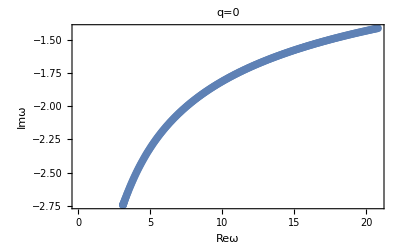

```mathematica
ListPlot[tabQNM1Ofkqzero,Frame->True,FrameLabel->{"Reω","Imω"},PlotLabel->"q=0"]
```

#### Example 7 Purely imaginary QNMs of set 2 (frequency in units of rH)

Zero momentum.

Note that the values provided further below and in the paper were obtained with a near horizon series expansion which contains 18 orders, a working precision of wp=30, precision and accuracy goals pg=ag=25. In order to reproduce these particular values, these values would have to be changed from their current values, and the file ``rulesHk14’’ would need to be replaced by a file that contains 18 instead of 14 near horizon expansion coefficients. However, the user may also simply verify the existence of these purely imaginary modes by choosing a large charge density and using one of the QNM frequencies provided below as inital values for the qnmRoutine[] search. At smaller and smaller charge densities, when the QNMs of set 2 are deep in the complex plane, they are more and more difficult to find, as they submerge in numerical noise produced by a boundary condition on the fluctuation which is equivalent to numerical infinity. See the appendix of reference [41] for a discussion of this point.

Example data obtained with lower accuracy, shorter computation time :
(order = 14, wp=25, pg = ag = 20)

```mathematica
qnmRoutine[0,-306/100,0,7/10]
```

{0,-3.059983694536463835467156}

```mathematica
nnMax=30;
tabFirstQNM=Table[0,{n,1,nnMax+1}];

For[nn=0,nn≤nnMax,nn++,
qnmRoutine[qnmVBC[[1,2]],qnmVBC[[2,2]],0,(7/10+nn/nnMax/100)];
tabFirstQNM[[(nn+1)]]={qnmVBC[[1,2]],qnmVBC[[2,2]]}
]
Clear[nnMax,nn]
```

```mathematica
tabLowestImaginaryQNM={{0,-3.059983694536463835467155872669850841738003501607389293791`25.},{0,-3.057128201969479348114112569043472802797407304137629335981`25.},{0,-3.054276927492522394498743437863323574406870281181896488642`25.},{0,-3.051429858484778088429011127149306401558157852279540213984`25.},{0,-3.048586982369538245523207284709274294792271819955809570262`25.},{0,-3.045748286614071727588287785022882477795743025485219748647`25.},{0,-3.042913758729494635057143799373757904551031727589697392294`25.},{0,-3.040083386270640356146270320907294611894288127989576736218`25.},{0,-3.037257156835929481290211224608324878713151102010039706553`25.},{0,-3.034435058067239591304662774976727956472964527119797223614`25.},{0,-3.03161707764977492762614313883439663364122900168211171366`25.},{0,-3.028803203311935952872975068483744849153624282414957852889`25.},{0,-3.025993422825188809869342394516465718936391310729469087066`25.},{0,-3.023187724003934687172320141312142832757114976218260759264`25.},{0,-3.020386094705379099040179445269094811950773668988137201358`25.},{0,-3.017588522829401087679368492256489341188139168919934985397`25.},{0,-3.014794996318422355507439400008818791004012059249071340657`25.},{0,-3.012005503157276335069512242182171951641518515668759745344`25.},{0,-3.009220031373077204146968449693289403931572492059000791876`25.},{0,-3.006438569035088853498759359411874206344865673323998346746`25.},{0,-3.003661104254593814578080503073708319918044762363968628652`25.},{0,-3.000887625184762154470191469550750252406408433649266388122`25.},{0,-2.998118120020520345200854852105617578803173818008807068374`25.},{0,-2.995352576998420114469236518700546993832656967177055586417`25.},{0,-2.992590984396507284764153726929936791568759810369985605298`25.},{0,-2.989833330534190607728284469587140294668560810503967312433`25.},{0,-2.987079603772110600541361680771008193601355861422315418891`25.},{0,-2.984329792512008391000476616732003466846362893494565634747`25.},{0,-2.981583885196594577883407137548680426389646064530544937352`25.},{0,-2.978841870309418113089373975103839776304264683667591771653`25.},{0,-2.976103736374735211960813029878818148407659951234163667718`25.}};
```

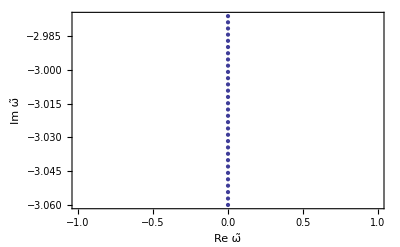

```mathematica
ListPlot[tabLowestImaginaryQNM,Frame->True,FrameLabel->{"Re ω̃","Im ω̃"}]
```

Example data obtained with higher accuracy, more horizon expansion terms, longer computation time :
(order = 18, wp=30, pg = ag = 25)

At q = 9/10 we find the following two modes :

```mathematica
qnmRoutine[0,-394/100,9/10]
```

{0,-3.95901666195004770316732458302}

```mathematica
qnmRoutine[0,-182/100,9/10]
```

{0,-1.81649857412707226654530837391}

At q = 10/10 we find the following two modes :

```mathematica
qnmRoutine[0,-14/10,10/10]
```

{0,-1.37827334431163008393571983537}

```mathematica
qnmRoutine[0,-28/10,10/10]
```

{0,-2.87215291598299510560714681221}

One way of looking at these imaginary QNM values is the following. Let us check if there are purely imaginary frequency values for which the absolute value of the bulk field vanishes at the boundary, i.e. Abs[ϕ[u_bdy]] =0. If this is the case, then we have found a QNM.

Here is a comic of how the zeros in the Abs[ϕ[u_bdy]] appear as q̃ is increased. On the horizontal axis we have the imaginary part of the frequency Im ω, and on the vertical axis we have the absolute value of the bulk field ϕ evaluated at the boundary. As q̃ is increased a zero crossing (i.e. a QNM) approaches from large negative imaginary frequency, as becoming apparent for q̃=0.6. One can follow this QNM with increasing q̃, and indeed see a second QNM appear around q̃=0.9. The poles appearing in the figures are located at known frequencies q̃, namely ⅈ n ((q̃)^2-2).

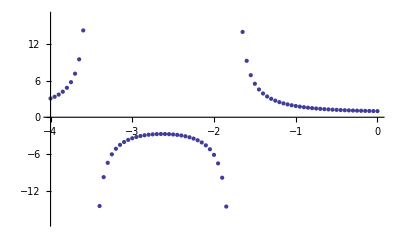

```mathematica
(*qt=0.5*)
```

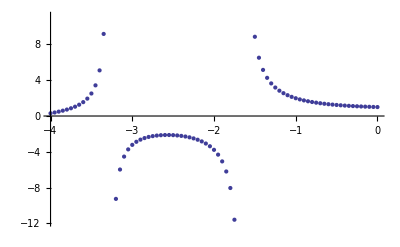

```mathematica
(*qt=0.6*)
```

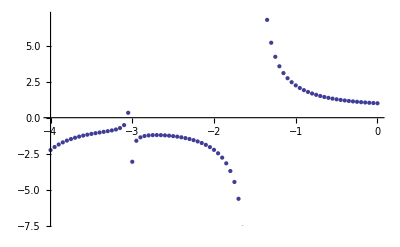

```mathematica
(*qt=0.7*)
```

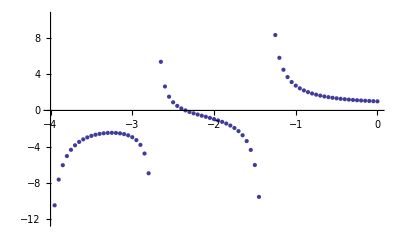

```mathematica
(*qt=0.8*)
```

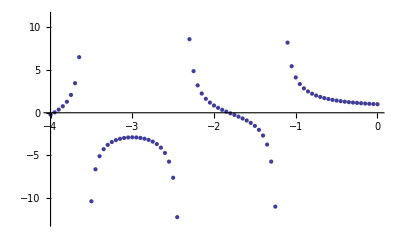

```mathematica
(*qt=0.9*)
```

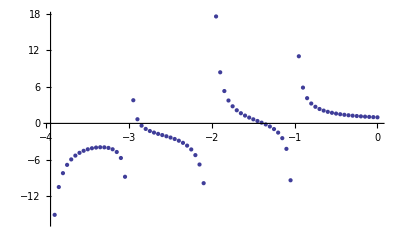

```mathematica
(*qt=1.0*)
```

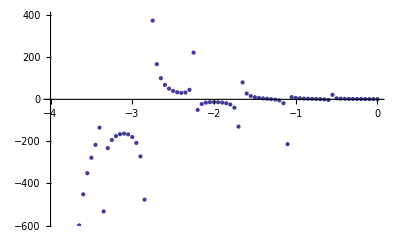

```mathematica
(*qt=1.2*)
```

Lowest imaginary QNM for RN AdS5 between q̃ = 0.7 and 0.8 :

```mathematica
tabFirstImaginaryQNMofqt=
{{0,-3.059983694536464004549876124788627601367987237050545181959`25.},{0,-3.042913758729495988778344559061490215599454032452390230239`25.},{0,-3.025993422825188958487060103961887436937459606096894345635`25.},{0,-3.009220031373078701913622357314553410521589072219709983507`25.},{0,-2.992590984396507775568919832959929791375860690826880532796`25.},{0,-2.976103736374735410591555059895120756068454180228580901911`25.},{0,-2.959755795223450176441867408609544314834236031951442915084`25.},{0,-2.94354472127566075295151489235731610909590634178616795319`25.},{0,-2.927468126264749896184140266465826393662747093553735689761`25.},{0,-2.911523672311281056827480819432830161648441326570444958175`25.},{0,-2.895709070915119659082710256725980660080844687026910534759`25.},{0,-2.880022081954167322812307186786439532676264350664744899615`25.},{0,-2.864460512690973602238908721860162264837592293784240369261`25.},{0,-2.84902221678834413463396412270617448190778800321404051159`25.},{0,-2.833705093334914394448902016602353300433018872790015223412`25.},{0,-2.818507085881638666886362590546602056159336813222702708863`25.},{0,-2.803426181489953485749949347074435691859447207550165594046`25.},{0,-2.788460409792296574192952301951318596353722294680531475807`25.},{0,-2.77360784206570019266404967471163647812863957422578985451`25.},{0,-2.758866590318863596398687380852789000523110921779912443157`25.},{0,-2.744234806393295057648871593905925181958641157707455441715`25.},{0,-2.729710681078809587879723593751843497261209739991264583838`25.},{0,-2.715292443243810775429527385945768823456041302399709970594`25.},{0,-2.700978358980538391997890123376206427613150740350162177508`25.},{0,-2.686766730765575506641936264484275159624535030512862430712`25.},{0,-2.672655896635724313078921303684115070957997566401158780611`25.},{0,-2.658644229379408025446547806149751233886329895130779458644`25.},{0,-2.644730135743645352062071875128060341111262912769024924908`25.},{0,-2.630912055656680544431214910098027552285483916543404575792`25.},{0,-2.617188461466216053592707865514683586292265782229136567537`25.},{0,-2.603557857193284474917042652223244674951757078125577110717`25.},{0,-2.590018777801640374435853537897911761414693030901152720473`25.},{0,-2.576569788482615074023998508334952244151759018385359179297`25.},{0,-2.563209483955377431971293724602099734708685301142708472297`25.},{0,-2.549936487782368255139433724683888426089969631551952438534`25.},{0,-2.536749451699851509397928421364617800498449893610906312914`25.},{0,-2.52364705496340074777158928033213647811221744641965745535`25.},{0,-2.510628003708073485711333048467460229852772554287498162245`25.},{0,-2.497691030323226967865740256305442553958049571312203202419`25.},{0,-2.484834892841580777806457426203136745454687309379871283049`25.},{0,-2.472058374342525066829319557532152863582346129349696387589`25.},{0,-2.459360282369233316898132327089512094886087593275319219122`25.},{0,-2.446739448359590304750804001636311925275236274433745392715`25.},{0,-2.434194727090422949444812741615432683578063736336984713596`25.},{0,-2.421724996135115796265897199370818717241078898694069006231`25.},{0,-2.409329155334062032222259789984765923553144143981687696653`25.},{0,-2.397006126277902765375035825533686148086965853039862545862`25.},{0,-2.384754851803248171607413928386877279765932331862824379553`25.},{0,-2.372574295500600325579223783178106974670953031921260785635`25.},{0,-2.360463441234281438861292449061655722646540576442367505868`25.},{0,-2.34842129267406393514148021181340780528708969917584356565`25.}};
```

The corresponding values of q̃ :

```mathematica
tabqt=
{0.7,0.702,0.704,0.706,0.708,0.71,0.712,0.714,0.716,0.718,0.72,0.722,0.724,0.726,0.728,0.73,0.732,0.734,0.736,0.738,0.74,0.742,0.744,0.746,0.748,0.75,0.752,0.754,0.756,0.758,0.76,0.762,0.764,0.766,0.768,0.77,0.7719999999999999,0.7739999999999999,0.7759999999999999,0.7779999999999999,0.7799999999999999,0.7819999999999999,0.7839999999999999,0.7859999999999999,0.7879999999999999,0.7899999999999999,0.7919999999999999,0.7939999999999999,0.7959999999999999,0.7979999999999999,0.7999999999999999};
```

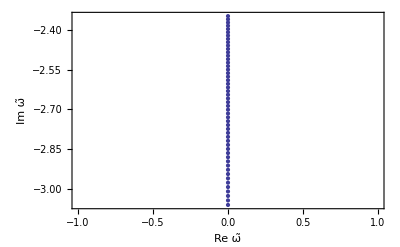

```mathematica
ListPlot[tabFirstImaginaryQNMofqt,Frame->True,FrameLabel->{"Re ω̃","Im ω̃"}]
```

### *** Attention! *** Vector QNMs : quit the kernel in order to perform the analogous calculation for the vector QNMs below.

```mathematica
Quit
```

### Set global parameters

Define precision and accuracy parameters:

>>>Adjust to desired accuracy and precision!

```mathematica
wp=25;(*Working precision.*)
ag=20;(*Accuracy goal.*)
pg=20;(*Precision goal*)

(* Constrain black brane charge: *)
$Assumptions={qt<Sqrt[2],qt>0};
```

### Fluctuation equation of motion (spin 1 vectors)

Usage, methods, parameter naming is analogous to the spin 2 tensor case described above.

This is the equation of motion for the vector fluctuation a_x as shown in equation (18):

```mathematica
myphiEqRS=(((-12 q^2 (-1+u) u^2 (-1+u (-1+q^2 u))+w^2) phi[u])/((-1+u)^2 u (1+u-q^2 u^2)^2)+(4 u (-2+q^2 (-2+3 u)) phi'[u])/((-1+u) (-1+u (-1+q^2 u)))+4 phi''[u])/4;
```

### Expansion near singular point (spin 1 vectors)

Usage, methods, parameter naming is analogous to the spin 2 tensor case described above.

#### Horizon

Compute indicial exponents :

```mathematica
phiIndH[u_]:=(1-u)^α
Solve[
0==Normal[Series[Simplify[(1-u)^(-α) (*phiEq*)myphiEqRS/.{phi->phiIndH}],{u,1,-2}]],
α]
indexRule=%[[2,1]]
```

{{α→-w/(2 √(-4+4 q^2-q^4))},{α→w/(2 √(-4+4 q^2-q^4))}}

α→w/(2 √(-4+4 q^2-q^4))

Define the near horizon expansion and plug it into the eom to get expansion coefficients:

```mathematica
order=14; 
phiH[u_]:=(1-u)^α Sum[cphiH[nn] (1-u)^nn,{nn,0,order}]/.indexRule
```

#### Find coefficients

```mathematica
coeffphiH[nnn_]:=Coefficient[Normal[Series[Simplify[(1-u)^(-α/.indexRule) myphiEqRS/.{phi->phiH}],{u,1,order}]],-1+u,nnn]//Simplify
```

Compute all the coefficients up to O(order) and write them into the list “ruleH”:
Replace the path variable in `SetDirectory[...]’ below with the path adequate for your system.

```mathematica
ruleH={};

For[iii=1,iii<order,iii++,
ruleH=Append[ruleH,Solve[0==coeffphiH[-2+iii]/.ruleH,cphiH[iii]][[1,1]]//Simplify]
]
SetDirectory["/Users/mkaminski3/Documents/Physics/Research/Quasinormal modes"]
Save["ruleaxHk14",ruleH]
```

/Users/mkaminski3/Documents/Physics/Research/Quasinormal modes

#### Readymade horizon expansion

Import the pre - calculated coefficients :

```mathematica
SetDirectory["/Users/mkaminski3/Documents/Physics/Research/Quasinormal modes"]
ruleH=Get["ruleaxHk14"];
```

/Users/mkaminski3/Documents/Physics/Research/Quasinormal modes

Define the horizon expansion (exclude the coeffient of O(order) which can' t be trusted) :

```mathematica
phiHExpansion[u_,c0_]:=SetPrecision[
phiH[u]/.ruleH/.{cphiH[0]->c0,cphiH[order]->0},wp]
(* Example: *)
phiHExpansion[1/2,1]/.{q->1/10,w->1/10,kk->0}
```

1.00699512921488853972648+0.010775376664466457762103 ⅈ

### Solutions (spin 1 vectors)

Usage, methods, parameter naming is analogous to the spin 2 tensor case described above.

Define numerical boundaries and solve the equation(s) of motion :

```mathematica
epsilon=1/1000000000;
uBnum=epsilon;
uHnum=1-1/10;
numericZero=0;

Clear[solphi]
solphi[omega_?NumericQ,kay_,kuh_,c0_]:=
Block[
{w=omega,kk=kay,q=kuh},
NDSolve[
{0==myphiEqRS,
phi[uHnum]==phiHExpansion[uHnum,c0],
phi'[uHnum]==(D[phiHExpansion[u,c0],u]/.{u->uHnum})},
phi[u],{u,uBnum,uHnum},
WorkingPrecision->wp,
AccuracyGoal->ag,
PrecisionGoal->pg,
MaxSteps->100000 
]
]

phiSol[w_?NumericQ,kuh_]:=Block[{q=kuh},SetPrecision[solphi[w,0,q,1][[1,1,2]],wp]]
```

### Quasinormal modes (spin 1 vectors)

Usage, methods, parameter naming is analogous to the spin 2 tensor case described above.

Routine for finding complex valued QNMs :

```mathematica
qnmRoutine[initWR_,initWI_,kuh_]:=Block[
{iWR=initWR,iWI=initWI,q=kuh},
eqQNMVBC[wR_?NumericQ,wI_?NumericQ]:=SetPrecision[Block[{w=wR+ⅈ wI},phiSol[w,q]/.u->uBnum],wp];
findQNMVBC[reWi_?NumericQ,imWi_?NumericQ]:=FindRoot[{Re[eqQNMVBC[wr,wi]]==numericZero,Im[eqQNMVBC[wr,wi]]==numericZero},{wr,reWi},{wi,imWi},WorkingPrecision->wp,
AccuracyGoal->ag,
PrecisionGoal->pg];qnmVBC=SetPrecision[findQNMVBC[iWR,iWI],wp];
Print[{qnmVBC[[1,2]],qnmVBC[[2,2]]}]
]
```

Routine for finding purely imaginary QNMs :

```mathematica
qnmImaginaryRoutine[initWI_,kuh_]:=Block[
{iWI=initWI,q=kuh},
eqQNMVBC[wI_?NumericQ]:=SetPrecision[Block[{w=ⅈ wI},phiSol[w,q]/.u->uBnum],wp];
findQNMVBC[imWi_?NumericQ]:=FindRoot[eqQNMVBC[wi]==numericZero,{wi,imWi},WorkingPrecision->wp,
AccuracyGoal->ag,
PrecisionGoal->pg];qnmVBC=SetPrecision[findQNMVBC[iWI],wp];
Print[qnmVBC[[1,2]]]
]
```

### Examples (spin 1 vectors)

Usage, methods, parameter naming is analogous to the spin 2 tensor case described above.

#### Example 8 Lowest vector QNM of Set 1 (complex valued) in units of temperature

Scan over the accessible range of charges :

```mathematica
(*turn off messages about precision issues: turn on for your information*)
Off[NDSolve::precw]
(*initialization*)
qnmRoutine[2,-2,0]
(*defining the temporary table*)
tabQNMTemp={};
(*running through increasing charge values*)
For[ss=0,ss<45,ss++,

qtTemp=Sqrt[2] ss/50;
qnmRoutine[qnmVBC[[1,2]],qnmVBC[[2,2]],qtTemp];
tabQNMTemp=Append[tabQNMTemp,{qnmVBC[[1,2]],qnmVBC[[2,2]]}/(Sqrt[uHt[qtTemp,1]] 2 π Tt[qtTemp,1])];
]
```

{1.9999999960000001803246,-2.000000004000000244437901}

{2.000409863387366945930251,-1.996919660441309022963602}

{2.001660951389254865097003,-1.987792399619793767503329}

{2.003811205694636371955165,-1.972946765672663598685917}

{2.006937976270032380794748,-1.952890569167544641880079}

{2.011116533042429292751002,-1.92826007905621352312423}

{2.016400869254166383399468,-1.899763629030420572135214}

{2.022811348650353287926294,-1.868128786649972241519394}

{2.030330507276927482834874,-1.834059505599841910339893}

{2.038905684283932676432007,-1.798206138707029795298288}

{2.048455910104462175486832,-1.761148104915092989810299}

{2.05888048071900761077978,-1.723387061386288119823545}

{2.070067325486029722160458,-1.68534767686362205629573}

{2.081900102875790095402199,-1.647383200652782547842183}

{2.094263632151830924140114,-1.609783558045331133747237}

{2.107047699306397730523756,-1.572784356416930546457318}

{2.120149491201869764032839,-1.536575774053132571991498}

{2.133474981298760675338403,-1.501310755148503533899273}

{2.146939578086087061702891,-1.467112244789403017943772}

{2.160468299163453181558277,-1.434079391647357703638553}

{2.173995676911325662174525,-1.402292755056107183437341}

{2.187465549179369482012367,-1.371818605076588455474218}

{2.200830845317333097613481,-1.342712420210081309694632}

{2.214053444454210152460395,-1.315021682060573471612411}

{2.227104157211408489247697,-1.288788048645265340834276}

{2.239962860944521201726585,-1.264048963708511294967339}

{2.25261879845545001568633,-1.240838731634433562118385}

{2.265071026672970699236606,-1.219189058900162960587559}

{2.277328970325863704063698,-1.199129036604436020201532}

{2.289412991266268020592483,-1.180684519851194002137024}

{2.301354823253225577673813,-1.163876858257099076484189}

{2.313197645745564931927469,-1.148720963061852944514859}

{2.324995490751107674755638,-1.135222781371737346193596}

{2.336811626793198815209527,-1.123376407692010293375058}

{2.348715605186724792899779,-1.113161299598101072224545}

{2.360778870045608097302931,-1.104540328692093429439856}

{2.373069285589024488255293,-1.097459550070935812812147}

{2.385645558003600034682395,-1.091850387679764014777625}

{2.398553021581966854165108,-1.087634227429213104163104}

{2.411822122961178447063226,-1.084728330666610043650195}

{2.425469872823709801659519,-1.083051243330645239660065}

{2.439502776006206780714744,-1.082526748869004569977861}

{2.45391284980945128762304,-1.083091147626728114485641}

{2.468536863992103590631996,-1.084706018646728343124244}

{2.48531486748891208529122,-1.082608391881678450063948}

```mathematica
tabQNM1={{0.9999999980000000901623001102908509333093616079777920823301`25.,-1.0000000020000001222189505597322507667854898360770355021731`25.},{1.0006051737631887484645112838387883239717223468341549769266`25.,-0.9988593739702426085252110691203421835977433988465670721369`25.},{1.0024343706877277970237394487931898051799744262835000878256`25.,-0.9954889821813871031166512818021197973752465307805312963539`25.},{1.0055254946279789100537763228792323759741610853594490511214`25.,-0.9900375179007745878592518563544066799005311726221563262903`25.},{1.0099325564965943945223167436292586978904776893277355920056`25.,-0.9827347872219930766304743630381299181625298617971968093762`25.},{1.0157154207284996428035362019366293790620485908206579776047`25.,-0.9738687267960674359213284298237439875384109970761138247064`25.},{1.0229306357823490175524896491461018794739240711696098347775`25.,-0.9637599579091013454419714085796779501593794176026429858081`25.},{1.0316255348074017176286690561524219690140695470489277414216`25.,-0.9527380592870115470825141991070143150101173498280349919767`25.},{1.0418362619442361878257768640174857947693740389859443074158`25.,-0.9411224885056660048952651587264013286021297435983566924287`25.},{1.0535891299524249051426244261905854564924152071210611497046`25.,-0.9292094557188041521797686006418846558867105898545726333446`25.},{1.0669041198460740497327252180131165441213454210116803273268`25.,-0.9172646379766109321928642933184816960257609564243771455899`25.},{1.0817993278262965588376313574209202840684943799969906232382`25.,-0.9055207342298697561073689348723279438085771278645808340316`25.},{1.0982954825371549884128067569201366968870349226468764369725`25.,-0.8941785212561662013453576011511323857543053835156532728901`25.},{1.1164200465871890258484551424143584611477649694844282165741`25.,-0.8834101247601794014597719269380791575515816404088387342488`25.},{1.136210737929595770475321995289335363519658688676644083515`25.,-0.8733634755020242696111312450902569290115084042556866295357`25.},{1.1577185161024163354526130343048646062691524046930735448583`25.,-0.8641672288005112892622624197898785109558615357682728715307`25.},{1.1810101889493481305887026284964327515613269108883921706967`25.,-0.8559357030153367713856386184849928076091881022325603291538`25.},{1.2061708397211446604129371526740329289802093289405458453249`25.,-0.8487736064837763081746227690689075252283932678638291375213`25.},{1.2333062833674672918789587785199403428525529301220534688362`25.,-0.8427804715012655204180674829956964993255234026271957932786`25.},{1.2625457568743882547675767792721821654294061323556242075806`25.,-0.8380548104531075874465598889767129449530372010915834822581`25.},{1.2940450457805509893895982981039787699909890079407545689602`25.,-0.8346980684857780853793697414185624530159076923677079780717`25.},{1.3279902556941291172974545953840132149992301504293968330264`25.,-0.8328184829265350021091659901588305071166115125914419261267`25.},{1.3646024586541003829448667739229202532896281665416470148547`25.,-0.8325349827691476374594689545270268664322377184711942188166`25.},{1.4041434832916096857308443264717342663260420306060046590591`25.,-0.8339812798456199084299915683056775272285515552880293322314`25.},{1.4469231790614660143241275017324411735866164451973063934102`25.,-0.8373103226645434906667592369620968384813860008053415020046`25.},{1.4933085739630141344843900873568153325143074074250883686701`25.,-0.8426993091390075299782258754261972257317805622974318910952`25.},{1.543735470432737126978021885303799530928068413072412364428`25.,-0.8503554904292993161447267789103099239463640177786900811033`25.},{1.5987231978211255641139230516356186198735180730510176375539`25.,-0.8605230511717694527015520366928495787274329941362684748424`25.},{1.6588934807152270571559575021613272676294154604306584687633`25.,-0.873491431092974956440510267292768816635946879531071678958`25.},{1.7249947191578270197351439612170577054059176709819202389335`25.,-0.8896055755358604597174684803003775186753780068309719574355`25.},{1.7979334556665824825576662390745843635649753734275072792658`25.,-0.9092787955133586535032726825373491324879907632980389359902`25.},{1.8788155017426615756395945073267806829663870952625253748169`25.,-0.9330092292575153870328614179293992944463202041005741392911`25.},{1.9690002462323066351250324056717620940071743782992446923779`25.,-0.9614014069882599476571781335821842516082492032977966152308`25.},{2.0701733050967388511778236147123279401140652120506946893777`25.,-0.9951952584089389558602569265507993103025055124960802048206`25.},{2.1844453173239627910154191252539464066534910490216431678287`25.,-1.0353062682274005508040782345311841374396197651734568741689`25.},{2.3144890882800079385322852077682100925280745360367757782754`25.,-1.0828826751883268916077018239984358662643015753683541932057`25.},{2.4637347234105320683713593429419005770315293746627030951879`25.,-1.1393890677646758853946708199879760681806352280373862204795`25.},{2.6366551259986737783846095944736821792986443055105561563138`25.,-1.206731197700888610496933436913649742974890032072819538759`25.},{2.8391962850165327345704408767778875159760728514147902348499`25.,-1.2874458184531405115567041744385214557832603877165279832316`25.},{3.0794460201240787117763361757874726607523472956734426988447`25.,-1.3849953149471527625768575141297315076985693397591162057107`25.},{3.3687081566995969467493315259006122451733606098831089072092`25.,-1.5042378379592294995278680999247426228390216276119839321655`25.},{3.7232948351743082733741514784882589615979516731292937334852`25.,-1.6522081026694208943496041395836108922648470120931310126335`25.},{4.1676508998122474314250003699138536829795540272608323881359`25.,-1.8394890414856116074824061611562016718173851162788375551103`25.},{4.7398941320892926087403920460767801967947772952816981478557`25.,-2.0827688530083109506993925161862066408010721561026792071499`25.},{5.5082333056048583450603280233436266696184463035743691523569`25.,-2.3993980316526561393261256332282714573658933645454312376548`25.}};
```

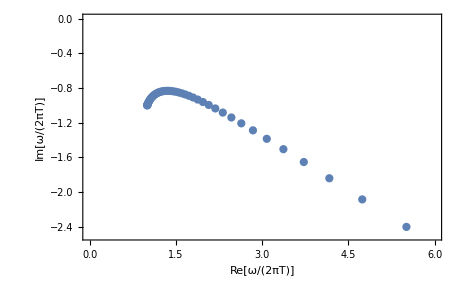

```mathematica
ListPlot[tabQNM1,PlotRange->{{0,6},{-2.5,0}},Frame->True,FrameLabel->{"Re[ω/(2πT)]","Im[ω/(2πT)]"}]
```

#### Example 9 Lowest vector QNM of Set 2 (purely imaginary) in units of temperature

```mathematica
(*initialization*)
qnmImaginaryRoutine[-18/10,Sqrt[2] 8/10]
(*defining temporary table*)
tabImQNMTemp={};
(*following the QNM while increasing charge density*)
For[ss=(4 40),ss<(4 45),ss++,
qtTemp=Sqrt[2] ss/(4 50);
qnmImaginaryRoutine[qnmVBC[[1,2]],qtTemp];
tabImQNMTemp=Append[tabImQNMTemp,qnmVBC[[1,2]]/(Sqrt[uHt[qtTemp,1]] 2 π Tt[qtTemp,1])];
]
```

-1.824279056850836166607541

-1.824279056850836166607541

-1.769244684386214243051134

-1.714926045058820553629503

-1.661302011486770261405787

-1.60835185360146974665432

-1.556055197830994430517008

-1.504391990807544499484893

-1.453342466243807910526969

-1.402887112874310675601118

-1.353006640140994355166039

-1.303681936240571251094769

-1.254894009549843126238012

-1.206664212481912880636937

-1.158912636288027575969372

-1.111651119157061669123612

-1.064865909122731781686845

-1.018546022153548014879998

-0.9726850664154493439778463

-0.9264285333082829026027633

-0.9501137532163735543781432

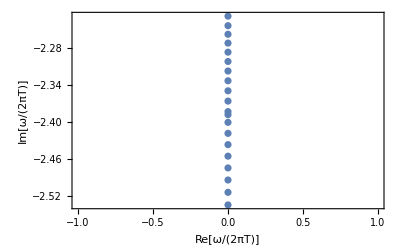

```mathematica
tabImQNM1=Table[{0,{-2.5337209122928280091771403839075397894709040132369699459764`25.,-2.513310156099459113646046141393758564442794056196978757681`25.,-2.4933498765030830962918048223120250617751376962922996865935`25.,-2.4738321963915870172076340248524399445778918226993549255162`25.,-2.4547494713087145095456654048898266404890667556174895769542`25.,-2.4360942431796390301636140634042881205140848182791677116439`25.,-2.417859194483356636909181397435456059652797668915792743421`25.,-2.4000371005595044348558650728408941487050832351618102256075`25.,-2.3826207759414243811160292150073094372875826824078693827739`25.,-2.3656030075023941868450724136762363090754500321564174492945`25.,-2.3489764616947229749455306153708266747581214420097456482506`25.,-2.3327335431728657426117894804272143123325331869414004996916`25.,-2.31694357235390338063927981761581682445046306128888832085`25.,-2.3014847309860541673505558880648741284856795769332909458998`25.,-2.286407073543935971048153177657915540583973843184927610296`25.,-2.2717139394618278009319358178879074630131775825211359726452`25.,-2.2574158292410195365248189029764209984742333728466012453093`25.,-2.2435360775353461976192972655826227586573379489045866368784`25.,-2.2280628506692710500306957526977852463366050040005895951021`25.,-2.3875204252201873460940902194083588576956156841141796512321`25.}[[nn]]},{nn,1,20}];
ListPlot[tabImQNM1,Frame->True,FrameLabel->{"Re[ω/(2πT)]","Im[ω/(2πT)]"}]
```

Following the first purely imaginary QNM down the axis to smaller charges :

```mathematica
Sqrt[2] ss/(6 50)
```

```mathematica
(*initialization*)
qnmImaginaryRoutine[-18/10,Sqrt[2] 8/10]
(*defining table*)
tabImQNMTemp={};
(*following the QNM while increasing charge density*)
For[ss=(6 40),ss>(6 30),ss--,
qtTemp=Sqrt[2] ss/(6 50);
qnmImaginaryRoutine[qnmVBC[[1,2]],qtTemp];
tabImQNMTemp=Append[tabImQNMTemp,qnmVBC[[1,2]]/(Sqrt[uHt[qtTemp,1]] 2 π Tt[qtTemp,1])];
]
```

-1.824279056850836166607541

-1.861376900528766735830131

-1.898808936141013114926243

-1.936581780453246678755589

-1.974702163655154799067249

-2.013176937999971016723372

-2.052013086983166551766669

-2.091217735044924347764692

-2.13079815777513385186533

-2.170761792594139554525806

-2.211116249877345211834367

-2.251869324487028363141333

-2.293029007670373027747999

-2.334603499278801702587403

-2.376601220260199933516598

-2.419030825372594436823314

-2.461901216065282447068048

-2.505221553471325803252457

-2.549001271453725674714412

-2.593250089646488588307729

-2.63797802643118732913431

-2.683195411789518974881206

-2.7289128999727783483925

-2.775141481930116193645114

-2.821892497438963272081967

-2.869177646883110364183695

-2.917009002626687631627341

-2.965399019935745643644204

-3.014360547403378738440759

-3.063906836839436642532603

-3.114051552591941870522876

-3.164808780274477758145003

-3.216193034882150983273151

-3.268219268288380937496367

-3.320902876125839994000014

-3.374259704067465576405992

-3.428306053537668356556735

-3.483058686899721372166716

-3.538534832182840436954164

-3.594752187431610234068814

-3.651728924781058669571558

-3.709483694382639913336714

-3.768035628329367504193187

-3.827404344751954430135829

-3.887609952281569606010654

-3.948673055098099996758776

-4.01061475880489530499575

-4.073456677391047147057132

-4.137220941559411726045501

-4.201930208711858799542839

-4.267607674891628089957525

-4.334277088985220200194735

-4.401962769482030400353403

-4.470689624078158848643516

-4.540483172390888803891795

-4.611369572021844909631393

-4.683375648169754728988301

-4.756528926948315071665554

-4.830857672511574547046079

-4.906390928029560522770267

-4.983158560492093205517055

-5.061191309250731611751282

-5.140520838139834809842665

```mathematica
(*ω/(2πT)*)
tabImQNMback=
{-2.5337209122928280091771403838851477925745398828512208248664`25.,-2.5475823633259680377248661083748573158040103526092949004424`25.,-2.5616501416940157744238191941102311727769191352946208291686`25.,-2.5759268162453400887943449501024999159958230421747023039849`25.,-2.590415035111997608384625765159067134527001828284733323028`25.,-2.6051175329978057728986837553477083009654090551517753672949`25.,-2.6200371386404067310606090231276827503851644331521986429485`25.,-2.6351767824205873722217564410453673813945050386442857600039`25.,-2.6505395040878212995892259933840017176876267671629634701041`25.,-2.6661284605675995511247923043148819374536861133341004210008`25.,-2.681946933813491496834138376762151760134948497393149223959`25.,-2.697998338664934538761947241052234067923629419904454818142`25.,-2.7142862306704226180729149882454267244849717583489977116518`25.,-2.7308143138349945833597548051991528377294301603142603743498`25.,-2.7475864482506678914871774534754925162080748123946658167571`25.,-2.764606657568679356369501240689058862063202055243451096297`25.,-2.7818791362730441471992306130567266168377421804947602188833`25.,-2.7994082567159906917225941000435434450437527087695405669045`25.,-2.817198575877238809366061275105345994959138599452545691405`25.,-2.8352548418108308383062712059460073930480858892792565531419`25.,-2.85358199974527475507317214148589529170844057090441603926`25.,-2.8721851978050941713564615499248888339291893884469469089417`25.,-2.8910697923244897277912820121781566132769587466190935809706`25.,-2.9102413527266954560376161854322808058696946817013129650294`25.,-2.9297056659457675166963943394699370774673903621364010564462`25.,-2.9494687403709872390237874695510514084385736271236718084751`25.,-2.9695368092978224464580205727235964970141806165849402402418`25.,-2.9899163338735084126277514350241840392049375944979259830287`25.,-3.0106140055298305049235208841857381359228921758863550598117`25.,-3.0316367479006717147247552476378962328140590229992871909022`25.,-3.0529917182273939907087018477689032033919935746378133689193`25.,-3.07468630826122107810024269772384826435972674328916546049`25.,-3.0967281446785517427099410080579760032050468817313339237202`25.,-3.1191250890326216238751350851590023061660113851063880715247`25.,-3.1418852372732066211841018905736977437590097221494226135941`25.,-3.1650169188751631253417333905361975676150728600842715310754`25.,-3.1885286956265516709047015228225176389828447770575286583996`25.,-3.2124293601378832519829935251650216533388561229606184364777`25.,-3.2367279341456179295661717144654161575269924358328808743086`25.,-3.2614336666953458846568805286503913434324392113959935073608`25.,-3.2865560323029528026144025706484511159934783727834908069518`25.,-3.312104729205317488445249106505616185687964336633911115889`25.,-3.3380896778254495962023270167357153878543760225710959552739`25.,-3.3645210195901222745426407829278556614047324978624697455196`25.,-3.3914091162505938327869000533752829209887567587686808851776`25.,-3.4187645498684848456785942549223717517654324840079851090141`25.,-3.4465981236387649668628974153368066163998016374904248520112`25.,-3.4749208637295429777174074512647082160549406242423002860323`25.,-3.5037440223233500389951737295873126350103833358688502197948`25.,-3.5330790820462573287884254246191382211314143744404408694986`25.,-3.5629377619688917263096219618783323847510880824602862655807`25.,-3.5933320253566740177373029485025444820372163109319360151295`25.,-3.6242740893349562356539652022897618764595776654097697629055`25.,-3.655776436617854449109742063368305207129003720439381519931`25.,-3.6878518294272975990024328182915882443362090873625941981129`25.,-3.7205133257011747365918901363263273736670491906636611796704`25.,-3.7537742976567213380677110154391098008317379568378370216798`25.,-3.7876484527379479787112229021696056402444034926646491127476`25.,-3.8221498569347502394168639300280613083303525180509631030717`25.,-3.8572929604173766754251821540058439225875628375260956843385`25.,-3.8930926253844478168101994171941800413553923708735422485358`25.,-3.9295641559772066897083748504464226402459220117410457149049`25.,-3.9667233300688072989045876132301746525677053549298678777956`25.};
```

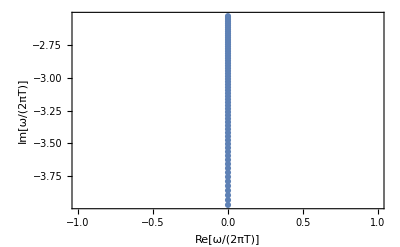

```mathematica
tabImQNM1back=Table[{0,tabImQNMback[[nn]]},{nn,1,Length[tabImQNMback]}];
ListPlot[tabImQNM1back,Frame->True,FrameLabel->{"Re[ω/(2πT)]","Im[ω/(2πT)]"}]
```

## Continued fraction method

```mathematica
Quit
```

Recall that the continued fraction method works with the equation of motion for tensor modes given in equation (55) in the text, as well as the rescaled frequency ω̃=ω/rH, momenta k̃=k/rH and charge q̃=q/(rH)^3. For the Reissner-Nordstrom the horizon radius is given by rH=(m/(1+q̃^2))^(1/4), and for the numerics we will work with m=1. This gives the relation between the two definitions of charge, q=q̃/(1+q̃^2)^(3/4). For brevity, the following code will make the definitions: K=k̃, Q=q̃, and om=ω̃. Although the specific case of the Reissner-Nordstrom black brane is treated here, the code is attempted to be generic enough to allow modification to any desired analytical solution.

### Definitions (spin 2 tensors)

This first block of definitions gives the momentum K, as well as the coefficients t_i, s_i, r_i that define the equation of motion in equation (55):

```mathematica
K=k(1+Q^2)^(1/4);t0=0;t1=-4;t2=4(-2+Q^2)(-4+5Q^2);t3=(-2+Q^2)^2(-20+72Q^2-40Q^4);t4=(-2+Q^2)^4(4-40Q^2+40Q^4);t5=(-2+Q^2)^6(8Q^2-20Q^4);t6=(-2+Q^2)^8 4Q^4;s0=-4/(-2+Q^2)(-2+I om+Q^2);s1=4(6-15Q^2+6Q^4+I om(-4+5Q^2));s2=4(-2+Q^2)(8-46Q^2+49Q^4-14Q^6-I om(5-18Q^2+10Q^4));s3=4(-2+27Q^2-45Q^4+16Q^6+I om(1-10Q^2+10Q^4))(-2+Q^2)^3;s4=-4Q^2(6-21Q^2+9Q^4+I om(-2+5Q^2))(-2+Q^2)^5;s5=4Q^4(-4+I om+2Q^2)(-2+Q^2)^7;r0=(-K^2(-2+Q^2)^2+om(om(4-5Q^2)+2I(-2-Q^2+Q^4)))/(-2+Q^2);r1=(K^2(-2+Q^2)^2(-1+2Q^2)+om(om(5-18Q^2+10Q^4)-2I(2+5Q^2-11Q^4+4Q^6)));r2=(-k^2Q^2(-2+Q^2)^2+om^2(-1+10Q^2-10Q^4)+6I om Q^2(2-5Q^2+2Q^4))(-2+Q^2)^2;r3=om Q^2(om(-2+5Q^2)-2I(2-9Q^2+4Q^4))(-2+Q^2)^4;r4=-om Q^4(om-2I(-2+Q^2))(-2+Q^2)^6;
```

This defines the initial coefficients c_i determining the series solution to the equation of motion, given in equation (57). c_0 is simply the normalization of the solution, while the others are determined by examining the equation of motion order by order in small r̃ at the horizon. Note that this implies that we will be dealing with m = 4 dimensional continued fractions when compared to the generic case of the Appendix :

```mathematica
c0=1;c1=Simplify[-c0 r0/s0];c2=Simplify[-(c1 r0+c0 r1+c1 s1)/(2s0+2t1)];c3=Simplify[-(c2 r0+c1 r1+c0 r2+2c2 s1+c1 s2+2c2 t2)/(3s0+3 2t1)];c4=Simplify[-(c3 r0+c2 r1+c1 r2+c0 r3+3c3 s1+2c2 s2+c1 s3+3 2c3 t2+2c2 t3)/(4s0+4 3t1)];
```

The 5 x5 (ie (m + 1) x (m + 1)) matrices defined here are related to the matrices P[n] given in equation (A1), which are defined in terms of the vector p[n] given in equation (58), (note : throughout these comments bracket, "[]", will represent labels of particular matrices, vectors, etc, while subscripts, e.g. "c_i", will indicate components of such objects). Here P2[n] = (n s_0 + n (n - 1) t_1) P[n], where the rescaling is done to improve numerics by removing a common demonimator.

```mathematica
P2[n_]:={{0,0,0,0,-(r4+(n-5)s5+(n-5)(n-6)t6)},{(n s0+n(n-1)t1),0,0,0,-(r3+(n-4)s4+(n-4)(n-5)t5)},{0,(n s0+n(n-1)t1),0,0,-(r2+(n-3)s3+(n-3)(n-4)t4)},{0,0,(n s0+n(n-1)t1),0,-(r1+(n-2)s2+(n-2)(n-3)t3)},{0,0,0,(n s0+n(n-1)t1),-(r0+(n-1)s1+(n-1)(n-2)t2)}};
```

We next define the main iterative procedue creating a continued fraction. Given the matrix P[n] of equation (A1), we define the 5 dimensional projective vector g[h, i] = P[h]*P[h + 1]* ... P[i - 1]*P[i]*(0, 0, 0, 0, 1) via matrix multiplication. Examining equation (A2), we see that the desired 4 dimensional continued factions have the components f[h]_j = lim_ {i -> \infinity} (g[h, i]_{j+1}/g[h, i]_1). Note that f[h] only depends on ratios of components of g[h, i]. Therefore the overall normalization does not matter, and the matrices P2[n] can be used instead of the P[n]. We calculate g[h, i] recursively : first define l[0] = (0, 0, 0, 0, 1); then define l[1] = P2[i]*l[0]; l[2] = P2[i - 1]*l[1]; etc; then g[h, i] = l[i - h]. For the purpose of calculating quasinormal modes we care about the continued fraction f[m + 1], as evident from Theorem 7/8 in equation (A3). For the Reissner - Nordstrom case at hand this implies we are interested in g[5, i]. This is accomplished by the following For loop, where for simplicity we start with Q = k = 0, and start with the iteration order i = 20 :

```mathematica
Block[{Q,k,i,h},k=0;Q=0;i=20;h=5;For[j=0;l={0,0,0,0,1},j<=i-h,j++,l=Simplify[P2[i-j].l]];g[h,i]=l;]
```

So far we have just made a bunch of definitions following from having an equation of motion on our hands. To calculate the quasinormal freqencies we must use Parusnikov's Theorem 7/8 which say such ω̃ will be roots of equation (59). Given the relation between g[h,i] and f[h] this equation can be written as the limit (under large i) of :

```mathematica
criteria[i_,h_]:=-c4 g[h,i][[5]]+(-g[h,i][[2]])c1+(-g[h,i][[3]])c2+(-g[h,i][[4]])c3+(-g[h,i][[1]]);
```

### Examples (spin 2 tensor)

We can now find a quasinormal mode. For example, the first two modes given in Table I, which have Q = k = 0, can easily be found by looking for roots to "criteria" in the complex plane. Starting the search somewhat nearby helps. :

```mathematica
Block[{Q,k,i,h},k=0;Q=0;i=20;h=5;sol=FindRoot[criteria[i,h],{om,3-I 3},WorkingPrecision->30,PrecisionGoal->7];Print[Simplify[om/N[(1+Q^2)^(1/4)]/.sol]];sol=FindRoot[criteria[i,h],{om,5-I 5},WorkingPrecision->30,PrecisionGoal->7];Print[Simplify[om/N[(1+Q^2)^(1/4)]/.sol]]];
```

3.11661-2.74887 ⅈ

5.14195-4.75524 ⅈ

These are fairly accurate, less than 0.5 % off of the results in Table I. Accuracy is increased by going to larger iteration order i. We can add another For loop to see how they move in the complex ω̃ plane. For example, i = {5, 10, 15, 20, 25, 30} :

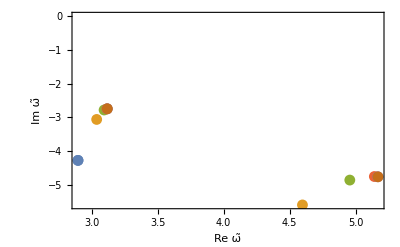

```mathematica
For[ii=1,ii≤6,ii++,Block[{Q,k,i,h},k=0;Q=0;i=5ii;h=5;For[j=0;l={0,0,0,0,1},j<=i-h,j++,l=Simplify[P2[i-j].l]];g[h,i]=l;sol1[ii]=FindRoot[criteria[i,h],{om,3-I 3},WorkingPrecision->30,PrecisionGoal->7];sol2[ii]=FindRoot[criteria[i,h],{om,5-I 5},WorkingPrecision->30,PrecisionGoal->7]]];Print[ListPlot[Table[{{Re[om/.sol1[i]],Im[om/.sol1[i]]},{Re[om/.sol2[i]],Im[om/.sol2[i]]}},{i,1,6}],Frame->True,FrameLabel->{"Re ω̃","Im ω̃"},PlotRange->All]]
```

We can use a For loop to vary different parameters, for example the charge. Stepping through Q=(0,7/10) in tenths show the behavior of the QNM with charge. Here we can see effect of the iteration order as well, as we run the procedure for i=20 (circle), 30 (triangle) and 40 (diamond). Note the increasing inaccuracy with increasing charge.

```mathematica
For[ii=2,ii≤4,ii++,For[qq=0,qq≤7,qq++,Block[{Q,k,i,h},k=0;Q=qq/10;i=10ii;h=5;For[j=0;l={0,0,0,0,1},j<=i-h,j++,l=Simplify[P2[i-j].l]];g[h,i]=l;sol1[ii,qq]=FindRoot[criteria[i,h],{om,3-I 3},WorkingPrecision->30,PrecisionGoal->7]]]];
```

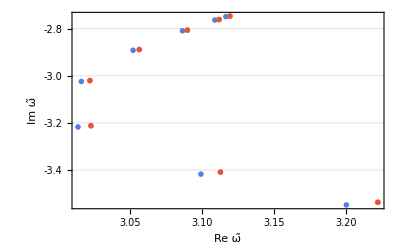

```mathematica
ListPlot[Table[{Re[om/.sol1[i,q]],Im[om/.sol1[i,q]]},{i,2,4},{q,0,7}],Frame->True,FrameLabel->{"Re ω̃","Im ω̃"},PlotTheme->"Business"]
```

Likewise the momentum can be varied. Higher order QNMs can be found by starting an educated search near their expected locations. Sometimes the WorkingPrecision and PrecisionGoal of the FindRoot need to be adjusted to obtain stable answers. The iteration order can be increased further to increase accuracy, at an exponential cost in run time. Modification to other black holes requires extracting the coefficient vector p[n] from the m+2 term recursion relation for the equation of motion, as defined in Theorem 2 of the Appendix. From this the (m+1)x(m+1) matrices P[n] can be defined and used to derive the required continued fraction to any desired accuracy. Enjoy!

### Definitions (spin 1 vectors)

For the spin 1 vector channel we will start with the equation of motion (18), but transform to the same radial coordinate as above: u=1-r̃(2-q̃^2)^2. We then strip off the near horizon in-falling behavior in the definition of eom2, and then extract the coefficients t_i, s_i, r_i.

```mathematica
eom=FullSimplify[(-12 Q^2 (-1+u) u^2 (-1+u (-1+Q^2 u))+om^2) g[u]+4 (-1+u) u (u (-2+Q^2 (-2+3 u)) (-1+u (-1+Q^2 u)) g'[u]+(-1+u) (1+u-Q^2 u^2)^2 g''[u])/.g[u]->g[r]/.g'[u]->-g'[r]/(2-Q^2)^2/.g''[u]->g''[r]/(2-Q^2)^4/.u->1-r(2-Q^2)^2]
```

(om^2+12 Q^2 (-2+Q^2)^3 r (-1+(-2+Q^2)^2 r)^2 (1+r (-2+Q^2 (5-2 Q^2+(-2+Q^2)^3 r)))) g[r]+4 (-2+Q^2)^2 r (1-(-2+Q^2)^2 r) (1+r (-2+Q^2 (5-2 Q^2+(-2+Q^2)^3 r))) ((-1+3 Q^2 (-2+Q^2) r) (-1+(-2+Q^2)^2 r) g'[r]+r (1+r (-2+Q^2 (5-2 Q^2+(-2+Q^2)^3 r))) g''[r])

```mathematica
eom2=Simplify[eom/r^(-I om/(2(2-Q^2)))/.g->Function[r,r^(-I om/(2(2-Q^2)))f[r]],0<q<Sqrt[2]];
```

```mathematica
ts=Simplify[Series[Coefficient[eom2/((2-Q^2)r),f''[r]],{r,0,10}]];ss=Simplify[Series[Coefficient[eom2/((2-Q^2)r),f'[r]],{r,0,10}]];rs=Simplify[Series[Coefficient[eom2,f[r]]/((2-Q^2)r),{r,0,10}]];t0=Coefficient[ts,r,0];t1=Coefficient[ts,r,1];t2=Coefficient[ts,r,2];t3=Coefficient[ts,r,3];t4=Coefficient[ts,r,4];t5=Coefficient[ts,r,5];t6=Coefficient[ts,r,6];s0=Coefficient[ss,r,0];s1=Coefficient[ss,r,1];s2=Coefficient[ss,r,2];s3=Coefficient[ss,r,3];s4=Coefficient[ss,r,4];s5=Coefficient[ss,r,5];r0=Coefficient[rs,r,0];r1=Coefficient[rs,r,1];r2=Coefficient[rs,r,2];r3=Coefficient[rs,r,3];r4=Coefficient[rs,r,4];
```

The rest of the definitions are the same as for the tensors. The c_i:

```mathematica
c0=1;c1=Simplify[-c0 r0/s0];c2=Simplify[-(c1 r0+c0 r1+c1 s1)/(2s0+2t1)];c3=Simplify[-(c2 r0+c1 r1+c0 r2+2c2 s1+c1 s2+2c2 t2)/(3s0+3 2t1)];c4=Simplify[-(c3 r0+c2 r1+c1 r2+c0 r3+3c3 s1+2c2 s2+c1 s3+3 2c3 t2+2c2 t3)/(4s0+4 3t1)];
```

P2[n] and criteria are the same as well:

```mathematica
P2[n_]:={{0,0,0,0,-(r4+(n-5)s5+(n-5)(n-6)t6)},{(n s0+n(n-1)t1),0,0,0,-(r3+(n-4)s4+(n-4)(n-5)t5)},{0,(n s0+n(n-1)t1),0,0,-(r2+(n-3)s3+(n-3)(n-4)t4)},{0,0,(n s0+n(n-1)t1),0,-(r1+(n-2)s2+(n-2)(n-3)t3)},{0,0,0,(n s0+n(n-1)t1),-(r0+(n-1)s1+(n-1)(n-2)t2)}};
```

The iterative procedue, with i=50 :

```mathematica
Block[{Q,k,i,h},k=0;Q=0;i=50;h=5;For[j=0;l={0,0,0,0,1},j<=i-h,j++,l=Simplify[P2[i-j].l]];g[h,i]=l;]
```

The citeria :

```mathematica
criteria[i_,h_]:=-c4 g[h,i][[5]]+(-g[h,i][[2]])c1+(-g[h,i][[3]])c2+(-g[h,i][[4]])c3+(-g[h,i][[1]]);
```

### Examples (spin 1 vector)

We can now find a quasinormal mode. For example, the first two modes given in Table V, which have Q  = 0, can easily be found by looking for roots to "criteria" in the complex plane. Starting the search somewhat nearby helps. (note the difference in units of frequency in Table V and that of om here :

```mathematica
Block[{Q,i,h},Q=0;i=50;h=5;sol=FindRoot[criteria[i,h],{om,2-I 2},WorkingPrecision->30,PrecisionGoal->7];Print[Simplify[om/N[(2-Q^2)]/.sol]];sol=FindRoot[criteria[i,h],{om,4-I 4},WorkingPrecision->30,PrecisionGoal->7];Print[Simplify[om/N[(2-Q^2)]/.sol]]];
```

1.-1. ⅈ

2.-2. ⅈ

Now increase Q some :

```mathematica
For[qq=0,qq≤6,qq++,Block[{Q,i,h},Q=qq/10;i=50;h=5;For[j=0;l={0,0,0,0,1},j<=i-h,j++,l=Simplify[P2[i-j].l]];g[h,i]=l;sol1[qq]=FindRoot[criteria[i,h],{om,2-I 2},WorkingPrecision->30,PrecisionGoal->7]]];
```

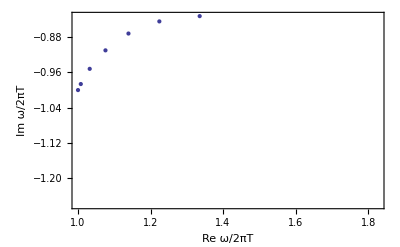

```mathematica
ListPlot[Table[{Re[om/N[(2-(q/10)^2)]/.sol1[q]],Im[om/N[(2-(q/10)^2)]/.sol1[q]]},{q,0,6}],Frame->True,FrameLabel->{"Re ω/2πT","Im ω/2πT"}]
```